```mathematica
Clear["Global`*"];
(*{x0Val,ℏωVal,aVal,εwoDivVal,εDivVal,NΔzVal,NΔxVal,IzVal,Wval}=ToExpression/@{"25","2.5","0","5","10","50","40","10","31.7"};

NΔzExtend=90;
NΔxExtend=50;*)

{x0Val,ℏωVal,aVal,εwoDivVal,εDivVal,NΔzVal,NΔxVal,IzVal,Wval}=ToExpression/@{"25","3.5","0","3","10","90","90","10","31.7"};

NΔzExtend=1400;
NΔxExtend=140;

εVal=N[εwoDivVal/εDivVal];

absdir=NotebookDirectory[];
dataDir=FileNameJoin[{absdir,"data"}];
If[!DirectoryQ[dataDir],
CreateDirectory[dataDir];
];

(* If the number of single electron wavefunctions we take into account in the full CI calculation is <= 40, b>=-12 in Sec. 2.1*)
bMin=-12;
(*nMax denotes the maximum value of n in the sum in Eq.B12. This has been checked numerically that by keeping maximum value of n = 2, the difference compared to keeping maximum value of n as infinity is negligible*)
nMax=2;

yOrbitalMax=3;

(*number of single particle orbitals taking into account for full CI calculations*)
(*numberOfSingParSt=6;*)
numberOfSingParSt=46;

(*Multielectron anti-symmetrized states for 2 electrons, Sz = 0*)
States=Tuples[Table[Table[{st},{st,1,numberOfSingParSt}],{2}]];

(*Multielectron anti-symmetrized states for 4 electrons, Sz = 0*)
(*States=Tuples[{Flatten[Table[Table[{sti,stj},{stj,sti+1,numberOfSingParSt}],{sti,1,numberOfSingParSt}],1],Flatten[Table[Table[{sti,stj},{stj,sti+1,numberOfSingParSt}],{sti,1,numberOfSingParSt}],1]}];*)

(*Multielectron anti-symmetrized states for 6 electrons, Sz = 0*)
(*States=Tuples[{Flatten[Table[Table[Table[{sti,stj,stk},{stk,stj+1,numberOfSingParSt}],{stj,sti+1,numberOfSingParSt}],{sti,1,numberOfSingParSt}],2],Flatten[Table[Table[Table[{sti,stj,stk},{stk,stj+1,numberOfSingParSt}],{stj,sti+1,numberOfSingParSt}],{sti,1,numberOfSingParSt}],2]}];*)
```

# 1. Tight-Binding calculations

```mathematica
xzGridToStProb[xGrid_,zGrid_,ζiζj_]:=Table[ζiζj[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];ρijPositionDomain[ζi_,ζj_]:=Conjugate[ζi]*ζj;
xzGridToWf[xGrid_,zGrid_,ζi_]:=Table[ζi[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

(*xGrid=Table[x,{x,-70,70,Δx}];
zGrid=Table[y,{y,-8,8.1,Δz}];*)
Length[xGrid]*Length[zGrid];
Length[xGrid];
Length[zGrid];
1/Length[xGrid] 1/Differences[xGrid][[1]];
1/Length[zGrid] 1/Differences[zGrid][[1]];

0.05/(1/Length[xGrid] 1/Differences[xGrid][[1]]);
0.05/(1/Length[zGrid] 1/Differences[zGrid][[1]]);
ηn[L_,n_,y_]:=(1/(π L^2))^(1/4) 1/Sqrt[2^n Factorial[n]] HermiteH[n,y/L]Exp[-(y^2/(2L^2))];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};
parameters=Join[parameters,{ω->ℏω/ℏmeVs(*s^-1*)}/.parameters];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*),LL->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-(W/2),
If[(z<=Iz/2+a/4)&&(z>=-(Iz/2)+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-(Iz/2)),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-(Iz/2)-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];
basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];

xMin=-xMax;
zMin=-zMax;

printStr="Parameters: "<>ToString[Flatten[{ToString/@{ℏω,x0,a,ε},ToString/@({ℏω,x0,a,ε}/.parameters)}ᵀ]];

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[ε/.parameters]},"_"];

SetDirectory[dataDir];
If[FileExistsQ[parastr<>"_evals.mx"]&&FileExistsQ[parastr<>"_evecs.mx"],
Print["Done before, skipped."];
Print[parastr<>"_evecs.mx"];

evals=Import[parastr<>"_evals.mx"];
evecs=Import[parastr<>"_evecs.mx"];
,
HxzTotal=Table[0,{Length[basis]},{Length[basis]}];
Do[
If[xzIndexToBasisInd[i,j+1]>Length[basis],
Continue[];
,
HxzTotal[[xzIndexToBasisInd[i,j+1],xzIndexToBasisInd[i,j]]]+=(t1/.parameters);
HxzTotal[[xzIndexToBasisInd[i,j],xzIndexToBasisInd[i,j+1]]]+=(t1/.parameters);
];

If[xzIndexToBasisInd[i,j+2]>Length[basis],
Continue[];
,
HxzTotal[[xzIndexToBasisInd[i,j+2],xzIndexToBasisInd[i,j]]]+=(t2/.parameters);
HxzTotal[[xzIndexToBasisInd[i,j],xzIndexToBasisInd[i,j+2]]]+=(t2/.parameters);
];

If[xzIndexToBasisInd[i+1,j]>Length[basis],
Continue[];
,
HxzTotal[[xzIndexToBasisInd[i+1,j],xzIndexToBasisInd[i,j]]]+=(t3/.parameters);
HxzTotal[[xzIndexToBasisInd[i,j],xzIndexToBasisInd[i+1,j]]]+=(t3/.parameters);
];

,{i,1,Length[xGrid]}
,{j,1,Length[zGrid]}
];

Do[
HxzTotal[[xzIndexToBasisInd[xi,zj],xzIndexToBasisInd[xi,zj]]]+=VQW Θij[xGrid[[xi]],zGrid[[zj]],W/.parameters,Iz/.parameters,a/.parameters]-(xGrid[[xi]] Fx+zGrid[[zj]] Fz )/.parameters;
,{xi,1,Length[xGrid]}
,{zj,1,Length[zGrid]}
];


(*Double well term*)
Do[
HxzTotal[[xzIndexToBasisInd[xi,zj],xzIndexToBasisInd[xi,zj]]]+=((Min[1/2 mt ω^2 ((xGrid[[xi]]+x0)nm)^2,1/2 mt ω^2 ((xGrid[[xi]]-x0)nm)^2])JtomeV)/.parameters;
,{xi,1,Length[xGrid]}
,{zj,1,Length[zGrid]}
];
(*Detuning term*)
HεVal=-(ε/(2(x0-(-x0))))x;
Do[
HxzTotal[[xzIndexToBasisInd[xi,zj],xzIndexToBasisInd[xi,zj]]]+=HεVal/.x->xGrid[[xi]]/.parameters;
,{xi,1,Length[xGrid]}
,{zj,1,Length[zGrid]}
];
Print["Start diagonalization \n"];
Print[printStr];

{evals,evecs}=Eigensystem[HxzTotal];
evecs=evecs[[Ordering[evals]]];
evals=evals[[Ordering[evals]]];

Print["Done Tight-Binding Calculations"];

SetDirectory[dataDir];
Export[parastr<>"_evals.mx",evals];
Export[parastr<>"_evecs.mx",evecs];
];
```

Done before, skipped.

xMin_-111.6_xMax_111.6_zMin_-6.7875_zMax_6.7875_a_0_hbarw_2.5_F_1.5_x0_25_detuning_0.5_evecs.mx

```mathematica
TBHamiltonianDiagonal=Table[Table[{x,z,((VQW Θij[x,z,W/.parameters,Iz/.parameters,a/.parameters])+(-(x Fx+z Fz ))+((Min[1/2 mt ω^2((x+x0)nm)^2,1/2 mt ω^2((x-x0)nm)^2])JtomeV))/.parameters},{x,xGrid}],{z,zGrid}];
```

```mathematica
(*Manipulate[Plot[((VQW Θij[x,z,W/.parameters,Iz/.parameters,a/.parameters])+(-(x Fx+z Fz ))+((Min[1/2 mt ω^2((x+x0)nm)^2,1/2 mt ω^2((x-x0)nm)^2])JtomeV))/.parameters,{z,Min[zGrid],Max[zGrid]},Frame->True,FrameLabel->{{"E (meV)",""},{"z (nm)",""}},PlotRange->{{Min[zGrid],Max[zGrid]},{0,250}}],{{x,0,"x (nm)"},Min[xGrid],Max[xGrid]}]*)
```

```mathematica
(*Manipulate[Plot[((VQW Θij[x,z,W/.parameters,Iz/.parameters,a/.parameters])+(-(x Fx+z Fz ))+((Min[1/2 mt ω^2((x+x0)nm)^2,1/2 mt ω^2((x-x0)nm)^2])JtomeV))/.parameters,{x,Min[xGrid],Max[xGrid]},Frame->True,FrameLabel->{{"E (meV)",""},{"x (nm)",""}},PlotRange->{{Min[xGrid],Max[xGrid]},{0,250}}],{{z,0,"z (nm)"},Min[zGrid],Max[zGrid]}]*)
```

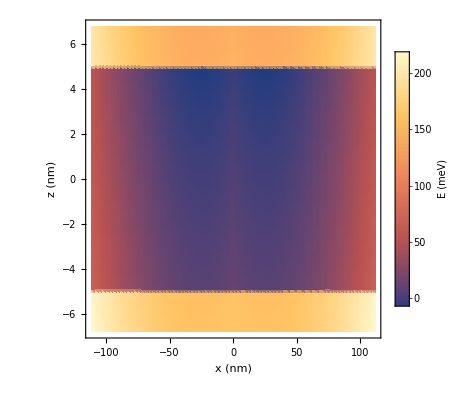

```mathematica
ListDensityPlot[Flatten[TBHamiltonianDiagonal,1],PlotLegends->BarLegend[Automatic,LegendLabel->"E (meV)"],FrameLabel->{{"z (nm)",""},{"x (nm)",""}},PlotRange->All]
```

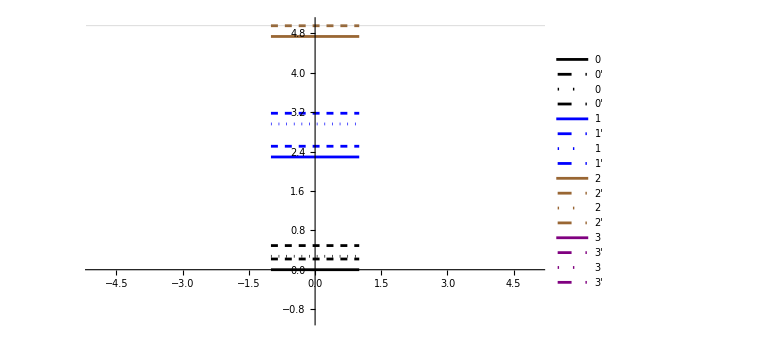

```mathematica
colorlist={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.6, 0.4, 0.2],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 0],RGBColor[0, 1, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.87, 0.94, 1],RGBColor[0.94, 0.91, 0.88],RGBColor[0.9, 1, 1],GrayLevel[0.85],RGBColor[0.88, 1, 0.88],RGBColor[1, 0.9, 1],RGBColor[1, 0.9, 0.8],RGBColor[1, 0.925, 0.925],RGBColor[0.94, 0.88, 0.94],RGBColor[1, 0.85, 0.85],RGBColor[1, 1, 0.85],GrayLevel[0, 0],GrayLevel[1],RGBColor[1, 1, 0]};
cutoff=10;
ListLinePlot[Table[Table[{x,evals⟦ind⟧-evals⟦1⟧},{x,-1,1,0.1}],{ind,1,60}],PlotStyle->Flatten[Table[{colorlist[[ind]],Directive[colorlist[[ind]],Dashed],Directive[colorlist[[ind]],Dotted],Directive[colorlist[[ind]],Dashed]},{ind,1,Length[colorlist]}]],PlotRange->{{-5,5},{-1,5}},PlotLegends->Flatten[Table[{ToString[ind],ToString[ind]<>"'",ToString[ind],ToString[ind]<>"'"},{ind,0,60}]],ImageSize->Large,GridLines->{{},{evals⟦cutoff⟧-evals⟦1⟧}}]
```

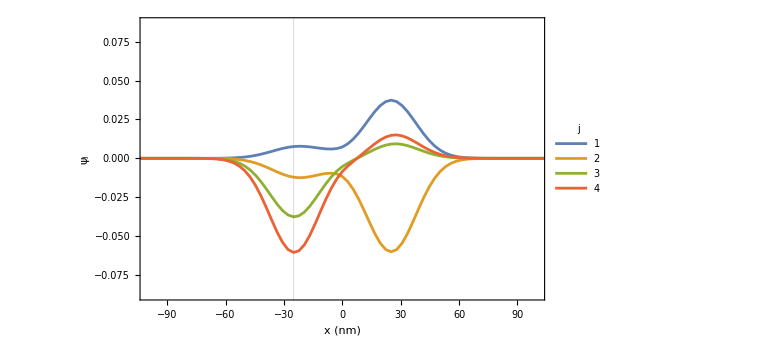

```mathematica
zPosition=0;

zInd=Position[Abs[Chop[zGrid-zPosition]],Min[Abs[Chop[zGrid-zPosition]]]][[1,1]];
ind=1;
ζ2Devec1=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+1]]];
ζ2Devec2=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+2]]];
ζ2Devec3=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+3]]];
ζ2Devec4=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+4]]];
ζ2DList={ζ2Devec1,ζ2Devec2,ζ2Devec3,ζ2Devec4};
ListPlot[{Table[{xGrid⟦xi⟧,ζ2Devec1⟦xi,zInd⟧},{xi,1,Length[xGrid]}],Table[{xGrid⟦xi⟧,ζ2Devec2⟦xi,zInd⟧},{xi,1,Length[xGrid]}],Table[{xGrid⟦xi⟧,ζ2Devec3⟦xi,zInd⟧},{xi,1,Length[xGrid]}],Table[{xGrid⟦xi⟧,ζ2Devec4⟦xi,zInd⟧},{xi,1,Length[xGrid]}]},Joined->True,PlotRange->{{-100,100},{1.1*Min[ζ2Devec1],1.1*Max[ζ2Devec1]}},ImageSize->Large,PlotLegends->LineLegend[Table[4*(ind-1)+i,{i,1,4}],LegendLabel->"j"],GridLines->{{-25},{}},Frame->True,FrameLabel->{{"ψ_j",""},{"x (nm)",""}}]
```

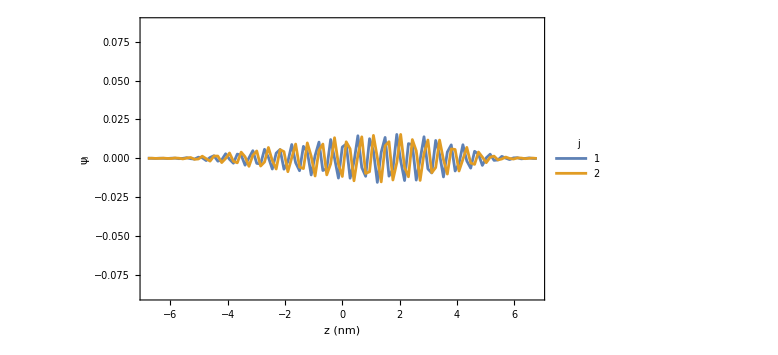

```mathematica
xPosition=0;

xInd=Position[Abs[Chop[xGrid-xPosition]],Min[Abs[Chop[xGrid-xPosition]]]][[1,1]];

ind=1;
ζ2Devec1=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+1]]];
ζ2Devec2=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+2]]];
ζ2Devec3=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+3]]];
ζ2Devec4=xzGridToWf[xGrid,zGrid,evecs[[4*(ind-1)+4]]];
ζ2DList={ζ2Devec1,ζ2Devec2,ζ2Devec3,ζ2Devec4};
ListPlot[{{zGrid,ζ2Devec1[[xInd]]}ᵀ,{zGrid,ζ2Devec2[[xInd]]}ᵀ},Joined->True,PlotRange->{{Min[zGrid],Max[zGrid]},{1.1*Min[ζ2Devec1],1.1*Max[ζ2Devec1]}},ImageSize->Large,PlotLegends->LineLegend[Table[4*(ind-1)+i,{i,1,4}],LegendLabel->"j"],GridLines->{{-25},{}},Frame->True,FrameLabel->{{"ψ_j",""},{"z (nm)",""}}]
```

# 2. Coulomb Integrals

## 2.1 Integration of the product of 0th order Bessel function and Hypergeometric functions

This evaluates ∫_0^D_c dr r J_0(|2π k r|)U(1/2,b,r^2/2 L^2) as function of k, where k=√(k_x^2+k_y^2)

HypergeometricUFValues[[x,y]] gives the list of values of ∫_0^D_c dr r J_0(|2π √(k_x^2+k_y^2) r|)U(1/2,b,r^2/2 L^2), where b=[-12,-11,-10,...,0,1]
while k_x=kxDomainRotateEx[[x]],k_y=kxDomainRotateEx[[y]]

```mathematica
ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-14(*m^3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->(*0.543*)aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4};
parameters=Join[parameters,{ω->ℏω/ℏmeVs(*s^-1*)}/.parameters];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*),LL->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

Clear[fFTijklAtkxkzFaster,fFTijklAtkxkz];
integrals[q_,L_,ΔrPerp_,LL_]:=If[EvenQ[q],Sqrt[π] LL^q Factorial2[q-1]HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)],0];
(*HypergeometricUF (supposed to be the built-in function HypergeometricU) is defined here such that no simplification is done on HypergeometricU*)
integralt[q_,L_,ΔrPerp_,LL_]:=If[EvenQ[q],LL^(q+1) Gamma[(1+q)/2]2^((q+1)/2),0];
integraly1Pny2Pm[n_,m_,L_,ΔrPerp_,LL_]:=1/2^(m+n+1) Sum[Binomial[n,k]Binomial[m,p](-1)^p integrals[n+p-k,L,ΔrPerp,LL]integralt[k+m-p,L,ΔrPerp,LL],{k,0,n},{p,0,m}];

(*
integraly1Pny2Pm[n,m,L,LL,ΔrPerp];
LL and L are the same variables. I distinguishes them to prevent a long symbolic expression generated by integraly1Pny2Pm;
L will remain symbolic for the evaluation of the numeric values of HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)] in the momentum domain,
while LL are numeric for those appear outside of the function HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)], e.g. those generated by integralt and part of the terms generated by integrals
*)
(* 
We need to know what functions of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] generated from integraly1Pny2Pm, with that information, we can directly replace the numeric values of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] in the symbolic expression generated by integraly1Pny2Pm;
Since only the second index is changing for different Subsuperscript[y, 1, n]Subsuperscript[y, 2, m], i.e. ((2-q)/2) = (2-n+p-k)/2, for k ∈ [0,n],p ∈ [0,m],
It is only necessary for us to record this information, as done by integraly1Pny2PmFunctionOfHypergeometricU;
I think this method is not that good (so I drop this for future use), since it seems like we need to run this function everytime we evaluate integraly1Pny2Pm in the momentum domain. We can just make a good guess on the minimum value of (2-q)/2 and just produce the numeric values of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] in the momentum domain in one go
*)
integraly1Pny2PmFunctionOfHypergeometricU[n_,m_]:=DeleteDuplicates[Flatten[Table[(2-(n+p-k))/2,{k,0,n},{p,0,m}]]];

integralJ0Ulimit0Infty[b_,kk_,L_]:=L^2/Sqrt[π] Gamma[2-b]HypergeometricU[2-b,3/2,2π^2 kk^2 L^2];
integralJ0ExpandUOrdernlimitDcInfty[kk_,L_,Dc_,n_]:=2^(-(1/2)+n) L^(1+2 n) Gamma[1/2-n] ((kk^(-1+2 n) π^(-1+2 n))/Gamma[1/2+n]-Dc^(1-2 n) HypergeometricPFQRegularized[{1/2-n},{1,3/2-n},-Dc^2 kk^2 π^2]);
integralJ0UlimitDcInfty[b_,L_,kk_,Dc_,nMax_]:=Sum[(-1)^-n (Pochhammer[1/2,n]Pochhammer[(1/2-b+1),n])/Factorial[n] integralJ0ExpandUOrdernlimitDcInfty[kk,L,Dc,n],{n,0,nMax}];
integralJ0Ulimit0Dc[b_,kk_,L_,Dc_,nMax_]:=If[Chop[kk]==0,
(* 
integralJ0Ulimit0Infty is indeterminate at k = 0;
But when I check it numerically, integralJ0Ulimit0Infty saturates at small k, typically k<10^-5;
Here, I take k=10^-9 for values at k=0
*)
2π(integralJ0Ulimit0Infty[b,10^-9,L]-integralJ0UlimitDcInfty[b,L,10^-9,Dc,nMax])
,
2π(integralJ0Ulimit0Infty[b,kk,L]-integralJ0UlimitDcInfty[b,L,kk,Dc,nMax])
];

fFTijklAtkxkz[iInd_,jInd_,kInd_,lInd_,kxVal_,kzVal_,parameters_,nMax_]:=Module[{cy1y2Term,y1y2Coeffs,y1y2CoeffsSA,nonzeroPos,nonzeroVal,HypergeometricUFValuesForCurrentk,fFTijklAtkxkz},
(* 
cy1y2Term = (Subscript[η, i]^*(Subscript[y, 1])Subscript[η, j](Subscript[y, 1])Subscript[η, k]^*(Subscript[y, 2])Subscript[η, l](Subscript[y, 2]))/ⅇ^(-(y1^2/L^2)-y2^2/L^2)=∑_(n,m) Subscript[c, n,m] Subscript[y, 1]^n Subscript[y, 2]^m;
We need to evaluate Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_(n,m) Subscript[c, nm]∫Subscript[dy, 1] Subscript[dy, 2] Subscript[y, 1]^n Subscript[y, 2]^m(ⅇ^(-(Subscript[y, 1]^2+Subscript[y, 2]^2)/L^2))/(√((Subscript[y, 1]-Subscript[y, 2])^2+Δr_⊥^2));
integraly1Pny2Pm[n,m,L,Subscript[Δr, ⊥]]=∫Subscript[dy, 1]Subscript[dy, 2]Subsuperscript[y, 1, n]Subsuperscript[y, 2, m]ⅇ^(-((Subscript[y, 1]^2+Subscript[y, 2]^2)/L^2))/Sqrt[(Subscript[y, 1]-Subscript[y, 2])^2+Subsuperscript[Δr, ⊥, 2]] ;

Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_(n,m) Subscript[c, nm] integraly1Pny2Pm[n,m,L,Δr_⊥];

Subscript[c, nm]=nonzeroVal⟦ind⟧;
n=nonzeroPos⟦ind,1⟧-1;
m=nonzeroPos⟦ind,2⟧-1;

Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_ind nonzeroVal⟦ind⟧integraly1Pny2Pm[nonzeroPos⟦ind,1⟧-1,nonzeroPos⟦ind,2⟧-1,L,Δr_⊥]
*)
cy1y2Term=ηn[L,iInd,y1]ηn[L,jInd,y1]ηn[L,kInd,y2]ηn[L,lInd,y2]/E^(-(y1^2/L^2)-y2^2/L^2);
y1y2Coeffs=CoefficientList[(cy1y2Term),{y1,y2}];

y1y2CoeffsSA=SparseArray[y1y2Coeffs];
nonzeroPos=y1y2CoeffsSA["NonzeroPositions"];
nonzeroVal=y1y2CoeffsSA["NonzeroValues"];

HypergeometricUFValuesForCurrentk=Table[HypergeometricUF[1/2,b,ΔrPerp^2/(2 L^2)]->integralJ0Ulimit0Dc[b,Sqrt[kxVal^2+kzVal^2],L/.parameters,Dc/.parameters,nMax],{b,1,1}];
(*Overscript[f, ~](Subscript[k, x],Subscript[k, z]) *)
fFTijklAtkxkz= Sum[(nonzeroVal[[ind]]/.parameters)(integraly1Pny2Pm[(nonzeroPos[[ind,1]]-1),(nonzeroPos[[ind,2]]-1),L,ΔrPerp,LL/.parameters]/.HypergeometricUFValuesForCurrentk),{ind,1,Length[nonzeroPos]}];

fFTijklAtkxkz
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

xGridExtend=Join[xGridExtend[[1;;(Length[xGridExtend]+1)/2]],Reverse[-xGridExtend[[1;;(Length[xGridExtend]+1)/2]]][[2;;-1]]];
zGridExtend=Join[zGridExtend[[1;;(Length[zGridExtend]+1)/2]],Reverse[-zGridExtend[[1;;(Length[zGridExtend]+1)/2]]][[2;;-1]]];

x0Ex=Max[xGridExtend];
z0Ex=Max[zGridExtend];

ksx=N[1/Δx];
ksz=N[1/Δz];

MMEx=Length[xGridExtend];
NNEx=Length[zGridExtend];

kxDomainEx=Table[m/(Length[xGridExtend]-1) 1/Differences[xGridExtend][[1]],{m,0,Length[xGridExtend]-1}];
kzDomainEx=Table[m/(Length[zGridExtend]-1) 1/Differences[zGridExtend][[1]],{m,0,Length[zGridExtend]-1}];

kxDomainRotateEx=Join[(kxDomainEx-1/Differences[xGridExtend][[1]]-Differences[kxDomainEx][[1]])[[Floor[Length[xGridExtend]/2]+2;;Length[xGridExtend]]],kxDomainEx[[1;;Floor[Length[xGridExtend]/2]+1]]];
kzDomainRotateEx=Join[(kzDomainEx-1/Differences[zGridExtend][[1]]-Differences[kzDomainEx][[1]])[[Floor[Length[zGridExtend]/2]+2;;Length[zGridExtend]]],kzDomainEx[[1;;Floor[Length[zGrid]/2]+1]]];

kxDomainRotateEx=Join[kxDomainRotateEx[[1;;Floor[Length[xGridExtend]/2]+1]],Reverse[-kxDomainRotateEx[[1;;Floor[Length[xGridExtend]/2]]]]];
kzDomainRotateEx=Join[kzDomainRotateEx[[1;;Floor[Length[zGridExtend]/2]+1]],Reverse[-kzDomainRotateEx[[1;;Floor[Length[zGridExtend]/2]]]]];

If[Length[Complement[Chop[Differences[Differences[kxDomainRotateEx]]],{0}]]=!=0,
Print["error 1"];
];
If[Length[Complement[Chop[Differences[Differences[kzDomainRotateEx]]],{0}]]=!=0,
Print["error 2"];
];

If[(Chop[kxDomainRotateEx[[-1]]-1/Differences[xGridExtend][[1]] 1/2]===0)&&(Chop[kxDomainRotateEx[[-1]]-1/Differences[xGridExtend][[1]] 1/2]===0)=!=True,
Print["error 3"];
];
If[(Chop[kzDomainRotateEx[[-1]]-1/Differences[zGridExtend][[1]] 1/2]===0)&&(Chop[kzDomainRotateEx[[-1]]-1/Differences[zGridExtend][[1]] 1/2]===0)=!=True,
Print["error 4"];
];
(*HypergeometricUFValuesForCurrentk=Table[HypergeometricUF[1/2,b,ΔrPerp^2/(2 L^2)]->integralJ0Ulimit0Dc[b,Sqrt[kxVal^2+kzVal^2],L/.parameters,Dc/.parameters,nMax],{b,1,1}];*)

(* 
Min[b]=1-n/2-Max[{m,n}]/2
The maximum power of y in Subscript[η, Subscript[i, y]](Subscript[y, 1]) is Subscript[i, y]
Since we have Subsuperscript[y, 1, m]Subsuperscript[y, 2, n] in the integrand Subsuperscript[η, Subscript[i, y], *](Subscript[y, 1])Subscript[η, Subscript[j, y]](Subscript[y, 1])Subsuperscript[η, Subscript[k, y], *](Subscript[y, 2])Subscript[η, Subscript[l, y]](Subscript[y, 2]), the maximum power of Subscript[y, 1] (Subscript[y, 2]) = m = Subscript[i, y]+Subscript[j, y] (n = Subscript[k, y]+Subscript[l, y])
b = 1-(n+p-k)/2, Max[p]=m, Max[k]=n, Max[m]=Subscript[i, y]+Subscript[j, y],Max[n]=Subscript[k, y]+Subscript[l, y], Max[p-k]=Max[{m,n}]=Max[{Subscript[i, y]+Subscript[j, y],Subscript[k, y]+Subscript[l, y]}]
Min[b]=1-(Max[n]+Max[p-k])/2=1-(Max[n]+Max[{m,n}])/2=1-(Subscript[k, y]+Subscript[l, y]+Max[{Subscript[i, y]+Subscript[j, y],Subscript[k, y]+Subscript[l, y]}])/2
*)
HypergeometricUFValues=Table["NA",{xi,1,Length[kxDomainRotateEx]},{zj,1,Length[kzDomainRotateEx]}];
```

```mathematica
SetDirectory[dataDir];
BesselJHypergeometricUIntLimit0DcValuesFileName=StringRiffle[{"solvedOddEvenOfdeltakCase","symNvePvexz","xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"bMin",ToString[bMin],"HypergeometricUFValues"},"_"]<>".mx";
If[FileExistsQ[BesselJHypergeometricUIntLimit0DcValuesFileName],
Print["Done before: "<>BesselJHypergeometricUIntLimit0DcValuesFileName];
,
SetSharedVariable[HypergeometricUFValues];
LaunchKernels[10];
ParallelDo[
Do[
Clear[clist];
clist=Table[{b,integralJ0Ulimit0Dc[b,Sqrt[kxDomainRotateEx[[xi]]^2+kzDomainRotateEx[[zj]]^2],L/.parameters,Dc/.parameters,nMax]},{b,bMin,1}];
If[AllTrue[Flatten[clist],NumericQ]=!=True,
Print["Non numeric: xi = "<>ToString[xi]<>", zj = "<>ToString[zj]];
Break[];
];
HypergeometricUFValues[[xi,zj]]={kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]],clist};

If[Mod[xi,100]==0,
Print["xi = "<>ToString[xi]<>"/"<>ToString[Length[kxDomainRotateEx]]<>", zj = "<>ToString[zj]<>"/"<>ToString[Length[kzDomainRotateEx]]];
];
,{xi,1,Length[kxDomainRotateEx]}
];
Print["zj = "<>ToString[zj]<>"/"<>ToString[Length[kzDomainRotateEx]]];
,{zj,1,Length[kzDomainRotateEx]}
];
SetDirectory[dataDir];
Export[BesselJHypergeometricUIntLimit0DcValuesFileName,HypergeometricUFValues];
];
```

## 2.2 Evaluating f_ijkl(Δr_⊥) (cf. description)

```mathematica
(* 
If you encounter the following error message
"Not numeric: zj = 1, xi = 1, {yiInd,yjInd,ykInd,ylInd}{10, 10, 10, 10}", that means 

This section evaluates B4, Subscript[f, ijkl](Δr_⊥), where i,j,k, and l indicates the index of part of the wavefunction in y direction. 
Since the wavefunction in 3D direction is separable, i.e. ϕ(x,y,z) = η(y)ζ(x,z), we can first perform the integration in y direction individually, and then perform the intergration in x-z direction

Hence fFTijklAtkxkzMatrixRotateEx stores with numerical value of Subscript[f, ijkl](Δr_⊥)
where, The coulomb integral Subscript[ϕ, i]^*(Subscript[r, 1])Subscript[ϕ, j](Subscript[r, 1])Subscript[ϕ, k](Subscript[r, 2])Subscript[ϕ, l]^*(Subscript[r, 2])e^2/(4 Subscript[πϵ, 0] Subscript[ϵ, r]|Subscript[r, 1]-Subscript[r, 2]|)=e^2/(4 Subscript[πϵ, 0] Subscript[ϵ, r])∫Subscript[dx, 1] Subscript[dz, 1] Subscript[dx, 2] Subscript[dz, 2] Subscript[ζ, Subscript[i, xz]]^*(Subscript[x, 1],Subscript[z, 1]) Subscript[ζ, Subscript[j, xz]](Subscript[x, 1],Subscript[z, 1])Subscript[ζ, Subscript[k, xz]]^*(Subscript[x, 2],Subscript[z, 2]) Subscript[ζ, Subscript[l, xz]](Subscript[x, 2],Subscript[z, 2])Subscript[f, ijkl](Δr_⊥)
and Δr_⊥=√((Subscript[x, 1]-Subscript[x, 2])^2+(Subscript[z, 1]-Subscript[z, 2])^2)
*)
```

```mathematica
ParallelDo[
Clear[fFTijklAtkxkzFaster,fFTijklAtkxkz];
ηn[L_,n_,y_]:=(1/(π L^2))^(1/4) 1/Sqrt[2^n Factorial[n]] HermiteH[n,y/L]Exp[-(y^2/(2L^2))];
integrals[q_,L_,ΔrPerp_,LL_]:=If[EvenQ[q],Sqrt[π] LL^q Factorial2[q-1]HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)],0];
integralsNumeric[q_,L_,ΔrPerp_,LL_,BesselJ2PiUIntLimit0Dc_]:=If[EvenQ[q],Sqrt[π] LL^q Factorial2[q-1]BesselJ2PiUIntLimit0Dc[{1/2,(2-q)/2,ΔrPerp^2/(2 L^2)}],0];
(*HypergeometricUF (supposed to be the built-in function HypergeometricU) is defined here such that no simplification is done on HypergeometricU*)
integralt[q_,L_,ΔrPerp_,LL_]:=If[EvenQ[q],LL^(q+1) Gamma[(1+q)/2]2^((q+1)/2),0];
integraly1Pny2Pm[n_,m_,L_,ΔrPerp_,LL_]:=1/2^(m+n+1) Sum[Binomial[n,k]Binomial[m,p](-1)^p integrals[n+p-k,L,ΔrPerp,LL]integralt[k+m-p,L,ΔrPerp,LL],{k,0,n},{p,0,m}];
integraly1Pny2PmNumeric[n_,m_,L_,ΔrPerp_,LL_,BesselJ2PiUIntLimit0Dc_]:=1/2^(m+n+1) Sum[Binomial[n,k]Binomial[m,p](-1)^p integralsNumeric[n+p-k,L,ΔrPerp,LL,BesselJ2PiUIntLimit0Dc]integralt[k+m-p,L,ΔrPerp,LL],{k,0,n},{p,0,m}];
(*
integraly1Pny2Pm[n,m,L,LL,ΔrPerp];
LL and L are the same variables. I distinguishes them to prevent a long symbolic expression generated by integraly1Pny2Pm;
L will remain symbolic for the evaluation of the numeric values of HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)] in the momentum domain,
while LL are numeric for those appear outside of the function HypergeometricUF[1/2,(2-q)/2,ΔrPerp^2/(2 L^2)], e.g. those generated by integralt and part of the terms generated by integrals
*)
(* 
We need to know what functions of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] generated from integraly1Pny2Pm, with that information, we can directly replace the numeric values of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] in the symbolic expression generated by integraly1Pny2Pm;
Since only the second index is changing for different Subsuperscript[y, 1, n]Subsuperscript[y, 2, m], i.e. ((2-q)/2) = (2-n+p-k)/2, for k ∈ [0,n],p ∈ [0,m],
It is only necessary for us to record this information, as done by integraly1Pny2PmFunctionOfHypergeometricU;
I think this method is not that good (so I drop this for future use), since it seems like we need to run this function everytime we evaluate integraly1Pny2Pm in the momentum domain. We can just make a good guess on the minimum value of (2-q)/2 and just produce the numeric values of HypergeometricUF[1/2,(2-q)/2,Δr^2/(2L^2)] in the momentum domain in one go
*)
integraly1Pny2PmFunctionOfHypergeometricU[n_,m_]:=DeleteDuplicates[Flatten[Table[(2-(n+p-k))/2,{k,0,n},{p,0,m}]]];

integralJ0Ulimit0Infty[b_,kk_,L_]:=L^2/Sqrt[π] Gamma[2-b]HypergeometricU[2-b,3/2,2π^2 kk^2 L^2];
integralJ0ExpandUOrdernlimitDcInfty[kk_,L_,Dc_,n_]:=2^(-(1/2)+n) L^(1+2 n) Gamma[1/2-n] ((kk^(-1+2 n) π^(-1+2 n))/Gamma[1/2+n]-Dc^(1-2 n) HypergeometricPFQRegularized[{1/2-n},{1,3/2-n},-Dc^2 kk^2 π^2]);
integralJ0UlimitDcInfty[b_,L_,kk_,Dc_,nMax_]:=Sum[(-1)^-n (Pochhammer[1/2,n]Pochhammer[(1/2-b+1),n])/Factorial[n] integralJ0ExpandUOrdernlimitDcInfty[kk,L,Dc,n],{n,0,nMax}];
integralJ0Ulimit0Dc[b_,kk_,L_,Dc_,nMax_]:=If[Chop[kk]==0,
(* 
integralJ0Ulimit0Infty is indeterminate at k = 0;
But when I check it numerically, integralJ0Ulimit0Infty saturates at small k, typically k<10^-5;
Here, I take k=10^-9 for values at k=0
*)
2π(integralJ0Ulimit0Infty[b,10^-9,L]-integralJ0UlimitDcInfty[b,L,10^-9,Dc,nMax])
,
2π(integralJ0Ulimit0Infty[b,kk,L]-integralJ0UlimitDcInfty[b,L,kk,Dc,nMax])
];

fFTijklAtkxkz[iInd_,jInd_,kInd_,lInd_,kxVal_,kzVal_,parameters_,nMax_]:=Module[{cy1y2Term,y1y2Coeffs,y1y2CoeffsSA,nonzeroPos,nonzeroVal,HypergeometricUFValuesForCurrentk,fFTijklAtkxkz},
(* 
cy1y2Term = (Subscript[η, i]^*(Subscript[y, 1])Subscript[η, j](Subscript[y, 1])Subscript[η, k]^*(Subscript[y, 2])Subscript[η, l](Subscript[y, 2]))/ⅇ^(-(y1^2/L^2)-y2^2/L^2)=∑_(n,m) Subscript[c, n,m] Subscript[y, 1]^n Subscript[y, 2]^m;
We need to evaluate Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_(n,m) Subscript[c, nm]∫Subscript[dy, 1] Subscript[dy, 2] Subscript[y, 1]^n Subscript[y, 2]^m(ⅇ^(-(Subscript[y, 1]^2+Subscript[y, 2]^2)/L^2))/(√((Subscript[y, 1]-Subscript[y, 2])^2+Δr_⊥^2));
integraly1Pny2Pm[n,m,L,Subscript[Δr, ⊥]]=∫Subscript[dy, 1]Subscript[dy, 2]Subsuperscript[y, 1, n]Subsuperscript[y, 2, m]ⅇ^(-((Subscript[y, 1]^2+Subscript[y, 2]^2)/L^2))/Sqrt[(Subscript[y, 1]-Subscript[y, 2])^2+Subsuperscript[Δr, ⊥, 2]] ;

Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_(n,m) Subscript[c, nm] integraly1Pny2Pm[n,m,L,Δr_⊥];

Subscript[c, nm]=nonzeroVal⟦ind⟧;
n=nonzeroPos⟦ind,1⟧-1;
m=nonzeroPos⟦ind,2⟧-1;

Subscript[f, ijkl][Subscript[Δr, ⊥]]=∑_ind nonzeroVal⟦ind⟧integraly1Pny2Pm[nonzeroPos⟦ind,1⟧-1,nonzeroPos⟦ind,2⟧-1,L,Δr_⊥]
*)
cy1y2Term=ηn[L,iInd,y1]ηn[L,jInd,y1]ηn[L,kInd,y2]ηn[L,lInd,y2]/E^(-(y1^2/L^2)-y2^2/L^2);
y1y2Coeffs=CoefficientList[(cy1y2Term),{y1,y2}];

y1y2CoeffsSA=SparseArray[y1y2Coeffs];
nonzeroPos=y1y2CoeffsSA["NonzeroPositions"];
nonzeroVal=y1y2CoeffsSA["NonzeroValues"];

HypergeometricUFValuesForCurrentk=Table[HypergeometricUF[1/2,b,ΔrPerp^2/(2 L^2)]->integralJ0Ulimit0Dc[b,Sqrt[kxVal^2+kzVal^2],L/.parameters,Dc/.parameters,nMax],{b,1,1}];
(*Overscript[f, ~](Subscript[k, x],Subscript[k, z]) *)
fFTijklAtkxkz= Sum[(nonzeroVal[[ind]]/.parameters)(integraly1Pny2Pm[(nonzeroPos[[ind,1]]-1),(nonzeroPos[[ind,2]]-1),L,ΔrPerp,LL/.parameters]/.HypergeometricUFValuesForCurrentk),{ind,1,Length[nonzeroPos]}];

fFTijklAtkxkz
];

fFTijklAtkxkzHypergeometricUFEvalExternally[iInd_,jInd_,kInd_,lInd_,kxVal_,kzVal_,parameters_,nMax_,HypergeometricUFValuesForCurrentk_]:=Module[{cy1y2Term,y1y2Coeffs,y1y2CoeffsSA,nonzeroPos,nonzeroVal,fFTijklAtkxkz},
cy1y2Term=ηn[L,iInd,y1]ηn[L,jInd,y1]ηn[L,kInd,y2]ηn[L,lInd,y2]/E^(-(y1^2/L^2)-y2^2/L^2);
y1y2Coeffs=CoefficientList[(cy1y2Term),{y1,y2}];

y1y2CoeffsSA=SparseArray[y1y2Coeffs];
nonzeroPos=y1y2CoeffsSA["NonzeroPositions"];
nonzeroVal=y1y2CoeffsSA["NonzeroValues"];

(*Overscript[f, ~](Subscript[k, x],Subscript[k, z]) *)
fFTijklAtkxkz= Sum[(nonzeroVal[[ind]]/.parameters)(integraly1Pny2Pm[(nonzeroPos[[ind,1]]-1),(nonzeroPos[[ind,2]]-1),L,ΔrPerp,LL/.parameters]/.HypergeometricUFValuesForCurrentk),{ind,1,Length[nonzeroPos]}];

fFTijklAtkxkz
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

fFTijklAtkxkzNumeric[iInd_,jInd_,kInd_,lInd_,kxVal_,kzVal_,parameters_,nMax_,BesselJ2PiUIntLimit0Dc_]:=Module[{cy1y2Term,y1y2Coeffs,y1y2CoeffsSA,nonzeroPos,nonzeroVal,fFTijklAtkxkz},
cy1y2Term=ηn[L,iInd,y1]ηn[L,jInd,y1]ηn[L,kInd,y2]ηn[L,lInd,y2]/E^(-(y1^2/L^2)-y2^2/L^2);
y1y2Coeffs=CoefficientList[(cy1y2Term),{y1,y2}];

y1y2CoeffsSA=SparseArray[y1y2Coeffs];
nonzeroPos=y1y2CoeffsSA["NonzeroPositions"];
nonzeroVal=y1y2CoeffsSA["NonzeroValues"];

(*Overscript[f, ~](Subscript[k, x],Subscript[k, z]) *)
fFTijklAtkxkz= Sum[(nonzeroVal[[ind]]/.parameters)(integraly1Pny2PmNumeric[(nonzeroPos[[ind,1]]-1),(nonzeroPos[[ind,2]]-1),L,ΔrPerp,LL/.parameters,BesselJ2PiUIntLimit0Dc]),{ind,1,Length[nonzeroPos]}];

fFTijklAtkxkz
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;
xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

xGridExtend=Join[xGridExtend[[1;;(Length[xGridExtend]+1)/2]],Reverse[-xGridExtend[[1;;(Length[xGridExtend]+1)/2]]][[2;;-1]]];
zGridExtend=Join[zGridExtend[[1;;(Length[zGridExtend]+1)/2]],Reverse[-zGridExtend[[1;;(Length[zGridExtend]+1)/2]]][[2;;-1]]];

x0Ex=Max[xGridExtend];
z0Ex=Max[zGridExtend];

ksx=N[1/Δx];
ksz=N[1/Δz];

MMEx=Length[xGridExtend];
NNEx=Length[zGridExtend];

kxDomainEx=Table[m/(Length[xGridExtend]-1) 1/Differences[xGridExtend][[1]],{m,0,Length[xGridExtend]-1}];
kzDomainEx=Table[m/(Length[zGridExtend]-1) 1/Differences[zGridExtend][[1]],{m,0,Length[zGridExtend]-1}];

kxDomainRotateEx=Join[(kxDomainEx-1/Differences[xGridExtend][[1]]-Differences[kxDomainEx][[1]])[[Floor[Length[xGridExtend]/2]+2;;Length[xGridExtend]]],kxDomainEx[[1;;Floor[Length[xGridExtend]/2]+1]]];
kzDomainRotateEx=Join[(kzDomainEx-1/Differences[zGridExtend][[1]]-Differences[kzDomainEx][[1]])[[Floor[Length[zGridExtend]/2]+2;;Length[zGridExtend]]],kzDomainEx[[1;;Floor[Length[zGrid]/2]+1]]];

kxDomainRotateEx=Join[kxDomainRotateEx[[1;;Floor[Length[xGridExtend]/2]+1]],Reverse[-kxDomainRotateEx[[1;;Floor[Length[xGridExtend]/2]]]]];
kzDomainRotateEx=Join[kzDomainRotateEx[[1;;Floor[Length[zGridExtend]/2]+1]],Reverse[-kzDomainRotateEx[[1;;Floor[Length[zGridExtend]/2]]]]];

If[Length[Complement[Chop[Differences[Differences[kxDomainRotateEx]]],{0}]]=!=0,
Print["error 1"];
];
If[Length[Complement[Chop[Differences[Differences[kzDomainRotateEx]]],{0}]]=!=0,
Print["error 2"];
];

If[(Chop[kxDomainRotateEx[[-1]]-1/Differences[xGridExtend][[1]] 1/2]===0)&&(Chop[kxDomainRotateEx[[-1]]-1/Differences[xGridExtend][[1]] 1/2]===0)=!=True,
Print["error 3"];
];
If[(Chop[kzDomainRotateEx[[-1]]-1/Differences[zGridExtend][[1]] 1/2]===0)&&(Chop[kzDomainRotateEx[[-1]]-1/Differences[zGridExtend][[1]] 1/2]===0)=!=True,
Print["error 4"];
];
(*HypergeometricUFValuesForCurrentk=Table[HypergeometricUF[1/2,b,ΔrPerp^2/(2 L^2)]->integralJ0Ulimit0Dc[b,Sqrt[kxVal^2+kzVal^2],L/.parameters,Dc/.parameters,nMax],{b,1,1}];*)

(* 
Min[b]=1-n/2-Max[{m,n}]/2
The maximum power of y in Subscript[η, Subscript[i, y]](Subscript[y, 1]) is Subscript[i, y]
Since we have Subsuperscript[y, 1, m]Subsuperscript[y, 2, n] in the integrand Subsuperscript[η, Subscript[i, y], *](Subscript[y, 1])Subscript[η, Subscript[j, y]](Subscript[y, 1])Subsuperscript[η, Subscript[k, y], *](Subscript[y, 2])Subscript[η, Subscript[l, y]](Subscript[y, 2]), the maximum power of Subscript[y, 1] (Subscript[y, 2]) = m = Subscript[i, y]+Subscript[j, y] (n = Subscript[k, y]+Subscript[l, y])
b = 1-(n+p-k)/2, Max[p]=m, Max[k]=n, Max[m]=Subscript[i, y]+Subscript[j, y],Max[n]=Subscript[k, y]+Subscript[l, y], Max[p-k]=Max[{m,n}]=Max[{Subscript[i, y]+Subscript[j, y],Subscript[k, y]+Subscript[l, y]}]
Min[b]=1-(Max[n]+Max[p-k])/2=1-(Max[n]+Max[{m,n}])/2=1-(Subscript[k, y]+Subscript[l, y]+Max[{Subscript[i, y]+Subscript[j, y],Subscript[k, y]+Subscript[l, y]}])/2
*)

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-14(*m^3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->(*0.543*)aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4};
parameters=Join[parameters,{ω->ℏω/ℏmeVs(*s^-1*)}/.parameters];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*),LL->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

SetDirectory[dataDir];

BesselJHypergeometricUIntLimit0DcValuesFileName=StringRiffle[{"solvedOddEvenOfdeltakCase","symNvePvexz","xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"hbarw",ToString[N[ℏω/.parameters]],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"bMin",ToString[bMin],"HypergeometricUFValues"},"_"]<>".mx";

If[!FileExistsQ[BesselJHypergeometricUIntLimit0DcValuesFileName],
Print["Current Directory: "<>Directory[]];
Print["File not found: "<>BesselJHypergeometricUIntLimit0DcValuesFileName];
Quit[];
];

HypergeometricUFValues=Import[BesselJHypergeometricUIntLimit0DcValuesFileName];
SetDirectory[dataDir];

parastr=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters]},"_"];
If[!DirectoryQ[parastr],
CreateDirectory[parastr];
];

SetDirectory[parastr];
fFTijklAtkxkzMatrixRotateExFileName=StringRiffle[Flatten[{"solvedOddEvenOfdeltakCase","symNvePvexz",{{"iInd","jInd","kInd","lInd"},{yiInd,yjInd,ykInd,ylInd}}ᵀ,parastr,"fFTijklAtkxkzMatrixRotateEx"}],"_"]<>".mx";

If[FileExistsQ[fFTijklAtkxkzMatrixRotateExFileName],
Print["Done before: {iInd,jInd,kInd,lInd} = "<>ToString[{yiInd,yjInd,ykInd,ylInd}]<>", "<>fFTijklAtkxkzMatrixRotateExFileName];
Continue[];
];
Print["Start: {yiInd,yjInd,ykInd,ylInd} = "<>ToString[{yiInd,yjInd,ykInd,ylInd}]];

fFTijklAtkxkzMatrixRotateEx=Table["NA",{xi,1,Length[kxDomainRotateEx]},{zj,1,Length[kzDomainRotateEx]}];
Do[
Do[
Clear[HypergeometricUFValuesForCurrentk];
HypergeometricUFValuesForCurrentk=Table[HypergeometricUF[1/2,b,ΔrPerp^2/(2 L^2)]->HypergeometricUFValues[[xi,zj,3]][[b-bMin+1,2]],{b,bMin,1}];

If[AllTrue[Table[(HypergeometricUFValues[[xi,zj,3]][[b-bMin+1,1]]===b)===True,{b,bMin,1}],TrueQ]=!=True,
Print["err 1, xi = "<>ToString[xi]<>", zj = "<>ToString[zj]<>", {yiInd,yjInd,ykInd,ylInd}"<>ToString[{yiInd,yjInd,ykInd,ylInd}]];
Abort[];
];

If[AllTrue[Chop[HypergeometricUFValues[[xi,zj]][[{1,2}]]-{kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]]}],PossibleZeroQ]=!=True,
Print["err 2, xi = "<>ToString[xi]<>", zj = "<>ToString[zj]<>", {yiInd,yjInd,ykInd,ylInd}"<>ToString[{yiInd,yjInd,ykInd,ylInd}]];
Abort[];
];

val=fFTijklAtkxkzHypergeometricUFEvalExternally[yiInd,yjInd,ykInd,ylInd,kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]],parameters,nMax,HypergeometricUFValuesForCurrentk];
If[NumericQ[val]=!=True,
val=N[val/.{ToString[ℏωVal]->ℏωVal}];
];
fFTijklAtkxkzMatrixRotateEx[[xi,zj]]={kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]],val};

If[NumericQ[val]=!=True,
Print["Not numeric: zj = "<>ToString[zj]<>", xi = "<>ToString[xi]<>", {yiInd,yjInd,ykInd,ylInd}"<>ToString[{yiInd,yjInd,ykInd,ylInd}]];
Print[val];
Quit[];
];

,{xi,1,Length[kxDomainRotateEx]}
];
If[Mod[zj,200]==0,
Print["zj = "<>ToString[zj]<>"/"<>ToString[Length[kzDomainRotateEx]]<>", {yiInd,yjInd,ykInd,ylInd}"<>ToString[{yiInd,yjInd,ykInd,ylInd}]];
];
,{zj,1,Length[kzDomainRotateEx]}
];
(* Slightly faster, but more complicated, just to be save, we'll use fFTijklAtkxkzHypergeometricUFEvalExternally *)
(*fFTijklAtkxkzMatrixRotateExNumeric=Table["NA",{xi,1,Length[kxDomainRotateEx]},{zj,1,Length[kzDomainRotateEx]}];
AbsoluteTiming[
Do[
Clear[BesselJ2PiUIntLimit0Dc];
BesselJ2PiUIntLimit0Dc=listRulesToAsso[Table[{1/2,b,ΔrPerp^2/(2 L^2)}->HypergeometricUFValues⟦xi,zj,3⟧⟦b-bMin+1,2⟧,{b,bMin,1}]];

If[AllTrue[Table[(HypergeometricUFValues⟦xi,zj,3⟧⟦b-bMin+1,1⟧===b)===True,{b,bMin,1}],TrueQ]=!=True,
Print["err 1, xi = "<>ToString[xi]<>", zj = "<>ToString[zj]];
Abort[];
];

If[AllTrue[Chop[HypergeometricUFValues⟦xi,zj⟧[[{1,2}]]-{kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]]}],PossibleZeroQ]=!=True,
Print["err 2, xi = "<>ToString[xi]<>", zj = "<>ToString[zj]];
Abort[];
];

clist={kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]],fFTijklAtkxkzNumeric[iInd,jInd,kInd,lInd,kxDomainRotateEx[[xi]],kzDomainRotateEx[[zj]],parameters,nMax,BesselJ2PiUIntLimit0Dc]};
If[NumericQ[clist[[3]]]=!=True,
Print["err 3, xi = "<>ToString[xi]<>", zj = "<>ToString[zj]];
Abort[];
];
fFTijklAtkxkzMatrixRotateExNumeric⟦xi,zj⟧=clist;

,{xi,1,Length[kxDomainRotateEx]}
,{zj,1,Length[kzDomainRotateEx]}
];
]*)
SetDirectory[absdir];
SetDirectory["data"];

parastr=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters]},"_"];
If[!DirectoryQ[parastr],
CreateDirectory[parastr];
];

SetDirectory[parastr];
fFTijklAtkxkzMatrixRotateExFileName=StringRiffle[Flatten[{"solvedOddEvenOfdeltakCase","symNvePvexz",{{"iInd","jInd","kInd","lInd"},{yiInd,yjInd,ykInd,ylInd}}ᵀ,parastr,"fFTijklAtkxkzMatrixRotateEx"}],"_"]<>".mx";
Export[fFTijklAtkxkzMatrixRotateExFileName,fFTijklAtkxkzMatrixRotateEx];

Print["Done: {iInd,jInd,kInd,lInd} = "<>ToString[{yiInd,yjInd,ykInd,ylInd}]<>", "<>fFTijklAtkxkzMatrixRotateExFileName];
,{yiInd,0,yOrbitalMax}
,{yjInd,0,yOrbitalMax}
,{ykInd,0,yOrbitalMax}
,{ylInd,0,yOrbitalMax}
];
```

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 0, 0}

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 0, 0}

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 0, 0}

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 0, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 0, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_0_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 0, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 0, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_0_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 0, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 0, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_0_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 0, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 0, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_0_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 1, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 1, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_1_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 1, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 1, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_1_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 1, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 2, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 1, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_1_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 2, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_2_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 1, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 2, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 1, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_1_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 2, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_2_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {0, 3, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {0, 3, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_0_jInd_3_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Done: {iInd,jInd,kInd,lInd} = {1, 3, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 2, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 2, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_2_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {1, 3, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {1, 3, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_1_jInd_3_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Done: {iInd,jInd,kInd,lInd} = {2, 3, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 2, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 2, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_2_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 0, 0}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 0, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_0_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 0, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 0, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_0_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 0, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 0, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_0_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 0, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 0, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_0_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 1, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 1, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_1_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 1, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 1, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_1_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 1, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 1, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_1_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 1, 3}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 1, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_1_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 2, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 2, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_2_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 2, 1}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {2, 3, 3, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 2, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_2_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 2, 2}

Done: {iInd,jInd,kInd,lInd} = {2, 3, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_2_jInd_3_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Done: {iInd,jInd,kInd,lInd} = {3, 3, 2, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_2_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 2, 3}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 2, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_2_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 3, 0}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 3, 0}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_3_lInd_0_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 3, 1}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 3, 1}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_3_lInd_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Start: {yiInd,yjInd,ykInd,ylInd} = {3, 3, 3, 2}

Done: {iInd,jInd,kInd,lInd} = {3, 3, 3, 2}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_3_lInd_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

Done before: {iInd,jInd,kInd,lInd} = {3, 3, 3, 3}, solvedOddEvenOfdeltakCase_symNvePvexz_iInd_3_jInd_3_kInd_3_lInd_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_hbarw_2.5_nMax_2_Dc_279_fFTijklAtkxkzMatrixRotateEx.mx

## 2.3 Coulomb Integrals

## evaluate individual Coulomb integrals

```mathematica
parts=5;
ParallelDo[
(*SetSharedVariable[iInd,jInd,absdir];*)
ijkIndList=Flatten[Table[{iInd,jInd,kInd},{iInd,1,numberOfSingParSt},{jInd,1,numberOfSingParSt},{kInd,1,numberOfSingParSt}],2];
Do[
{iInd,jInd,kInd}=ijkIndList[[ind]];
If[Ordering[{iInd,jInd}]==={2,1},
Print["No need to evaluate since {iInd,jInd} = "<>ToString[{iInd,jInd}]];
Continue[];
];

(*LaunchKernels[noOfCores];
ParallelDo[*)
ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

Length[xGrid]*Length[zGrid];
Length[xGrid];
Length[zGrid];
1/Length[xGrid] 1/Differences[xGrid][[1]];
1/Length[zGrid] 1/Differences[zGrid][[1]];

0.05/(1/Length[xGrid] 1/Differences[xGrid][[1]]);
0.05/(1/Length[zGrid] 1/Differences[zGrid][[1]]);
ηn[L_,n_,y_]:=(1/(π L^2))^(1/4) 1/Sqrt[2^n Factorial[n]] HermiteH[n,y/L]Exp[-(y^2/(2L^2))];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];

parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};
parameters=Join[parameters,{ω->ℏω/ℏmeVs(*s^-1*)}/.parameters];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*),LL->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-(W/2),
If[(z<=Iz/2+a/4)&&(z>=-(Iz/2)+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-(Iz/2)),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-(Iz/2)-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

numberOfCoreToNumberOfSingParSt[n_]:=2*n*(n+1);
basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];

xzGridToStProb[xGrid_,zGrid_,ζiζj_]:=Table[ζiζj[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];ρijPositionDomain[ζi_,ζj_]:=Conjugate[ζi]*ζj;

xMin=-xMax;
zMin=-zMax;

SetDirectory[dataDir];
parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];

If[!FileExistsQ[parastr<>"_evals.mx"],
Print["File not found:"<>parastr<>"_evals.mx"];
Abort[];
];
If[!FileExistsQ[parastr<>"_evecs.mx"],
Print["File not found:"<>parastr<>"_evecs.mx"];
Abort[];
];

evals=Import[parastr<>"_evals.mx"];
evecs=Import[parastr<>"_evecs.mx"];

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd[[ind]]->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd[[ind]]->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals[[1]],{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals[[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd][[{1,3}]]]]]+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd][[2]]]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

(*If[AllTrue[Table[AllTrue[Table[(ToExpression[StringSplit[stateIndToOrbitalxyValleyzInd[stInd][[1]],""][[3]]]+ToExpression[stateIndToOrbitalxyValleyzInd[stInd][[2]]])<=(numberOfCore-1),{stInd,1,numberOfCoreToNumberOfSingParSt[numberOfCore]}],TrueQ],{numberOfCore,1,6}],TrueQ]=!=True,
Print["Definition of core orbitals need to be refined"];
];*)

(*numberOfCore=6;*)
(*numberOfSingParSt=numberOfCoreToNumberOfSingParSt[numberOfCore];*)

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{dataDir,"CoulombIntegral",parastrextend}];
If[!DirectoryQ[parastrextendDir],
CreateDirectory[parastrextendDir];
];

SetDirectory[parastrextendDir];

CoulombcijIndDir=FileNameJoin[{parastrextendDir,StringRiffle[ToString/@{"CoulombcijInd","i",iInd},"_"]}];
If[!DirectoryQ[CoulombcijIndDir],
CreateDirectory[CoulombcijIndDir];
];

SetDirectory[CoulombcijIndDir];
CoulombcijIndFileName=StringRiffle[ToString/@{"CoulombcijInd","i",iInd,"j",jInd,"k",kInd,parastrextend},"_"]<>".mx";
If[FileExistsQ[CoulombcijIndFileName],
Print["Done before: "<>CoulombcijIndFileName];
Continue[];
];

Print["Start:"<>CoulombcijIndFileName];
CoulombcijInd=Table["NA",{lInd,1,numberOfSingParSt}];

Do[

If[(Ordering[{iInd,jInd}]==={2,1})||(Ordering[{kInd,lInd}]==={2,1}),
Continue[];
];

yiInd=stateIndToOrbitalxyValleyzInd[iInd][[2]];
yjInd=stateIndToOrbitalxyValleyzInd[jInd][[2]];
ykInd=stateIndToOrbitalxyValleyzInd[kInd][[2]];
ylInd=stateIndToOrbitalxyValleyzInd[lInd][[2]];

ρ1ij=ρijPositionDomain[evecs[[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[iInd][[{1,3}]]]]],evecs[[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[jInd][[{1,3}]]]]]];
ρ2ij=ρijPositionDomain[evecs[[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[kInd][[{1,3}]]]]],evecs[[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[lInd][[{1,3}]]]]]];

ρ1ij2D=xzGridToStProb[xGrid,zGrid,ρ1ij];
ρ2ij2D=xzGridToStProb[xGrid,zGrid,ρ2ij];

x0Ex=Max[xGridExtend];
z0Ex=Max[zGridExtend];


ksx=N[1/Δx];
ksz=N[1/Δz];

MMEx=Length[xGridExtend];
NNEx=Length[zGridExtend];

x0=Max[xGrid];
z0=Max[zGrid];

MM=Length[xGrid];
NN=Length[zGrid];

xStartIndInExtend=Position[Chop[xGridExtend-xGrid[[1]]],0][[1,1]];
zStartIndInExtend=Position[Chop[zGridExtend-zGrid[[1]]],0][[1,1]];

ρ1ij2DExtend=Table[0,{Length[xGridExtend]},{Length[zGridExtend]}];
Do[
ρ1ij2DExtend[[xStartIndInExtend+xi-1,zStartIndInExtend+zj-1]]=ρ1ij2D[[xi,zj]]
,{xi,1,Length[xGrid]}
,{zj,1,Length[zGrid]}
];
Clear[ρ1ij2D];

ρ2ij2DExtend=Table[0,{Length[xGridExtend]},{Length[zGridExtend]}];
Do[
ρ2ij2DExtend[[xStartIndInExtend+xi-1,zStartIndInExtend+zj-1]]=ρ2ij2D[[xi,zj]]
,{xi,1,Length[xGrid]}
,{zj,1,Length[zGrid]}
];
Clear[ρ2ij2D];

SetDirectory[dataDir];

parastrft=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters]},"_"];
If[!DirectoryQ[parastrft],
Print["Dir not found:"];
Print[parastrft];
Abort[];
];
SetDirectory[parastrft];
fFTijklAtkxkzMatrixRotateExFileName=StringRiffle[Flatten[{"solvedOddEvenOfdeltakCase","symNvePvexz",{{"iInd","jInd","kInd","lInd"},{yiInd,yjInd,ykInd,ylInd}}ᵀ,parastrft,"fFTijklAtkxkzMatrixRotateEx"}],"_"]<>".mx";
If[!FileExistsQ[fFTijklAtkxkzMatrixRotateExFileName],
Print["File not found: "<>fFTijklAtkxkzMatrixRotateExFileName];
Abort[];
];
(*fFTijklAtkxkzMatrixRotateEx=Import[fFTijklAtkxkzMatrixRotateExFileName,"Dataset1"];*)
fFTijklAtkxkzMatrixRotateEx=Import[fFTijklAtkxkzMatrixRotateExFileName][[All,All,3]];

(* Here, we assume the domain of ρt in position is x∈[0,2* xMax],z∈[0,2* zMax] so we don't need to care about the phase shift when approximating a countinous FT into a DFT*)
ρt=Fourier[ρ1ij2DExtend];

(* fFTijklAtkxkzNIntMatrixRotateEx, the domain is  kx∈[-kxMax,kxMax],kz∈[-kzMax,kzMax]*)
(* fFTijklAtkxkzNIntMatrixRotateExBack, the domain is  kx∈[0,2*kxMax],kz∈[0,2*kzMax]*)

fFTijklAtkxkzMatrixRotateExBack=Transpose[RotateLeft[Transpose[fFTijklAtkxkzMatrixRotateEx],Floor[Length[zGridExtend]/2]]];
fFTijklAtkxkzMatrixRotateExBack=RotateLeft[fFTijklAtkxkzMatrixRotateExBack,Floor[Length[xGridExtend]/2]];

(* Vx2z2DFT, the domain is  kx∈[0,2*kxMax],kz∈[0,2*kzMax]*)
(*Vx2z2DFT=
Table[ediv4πε0εr*ρt[[xi,zj]]*fFTijklAtkxkzMatrixRotateExBack[[xi,zj,3]]/10^-9,{xi,1,Length[xGridExtend]},{zj,1,Length[zGridExtend]}];*)
Vx2z2DFT=(ediv4πε0εr/10^-9)ρt*fFTijklAtkxkzMatrixRotateExBack;

(* Vx2z2, the domain is  x∈[0,2*xMax],z∈[0,2*zMax]*)
(* Based on the original assumption that the domain of ρ2ij2DExtend in position is x∈[0,2* xMax],z∈[0,2* zMax]*)
Vx2z2=InverseFourier[Vx2z2DFT];

CoulombIntegral=Total[Flatten[ρ2ij2DExtend*Vx2z2]];

If[NumericQ[CoulombIntegral]=!=True,
Print["not numeric: {kInd,lInd} = "<>ToString[{kInd,lInd}]];
Quit[];
];
CoulombcijInd[[lInd]]={{iInd,jInd,kInd,lInd},CoulombIntegral};
(*Print["kInd = "<>ToString[kInd]<>"/"<>ToString[numberOfSingParSt]<>", lInd = "<>ToString[lInd]<>"/"<>ToString[numberOfSingParSt]];*)
,{lInd,1,numberOfSingParSt}
];

SetDirectory[CoulombcijIndDir];

CoulombcijIndFileName=StringRiffle[ToString/@{"CoulombcijInd","i",iInd,"j",jInd,"k",kInd,parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
Export[CoulombcijIndFileName,CoulombcijInd];
Print["Done:"<>CoulombcijIndFileName];
Print["Done: "<>ToString[ind]<>"/"<>ToString[Length[ijkIndList]]];

,{ind,part,Length[ijkIndList],parts}
];
,{part,1,parts}
];
```

Start:CoulombcijInd_i_1_j_1_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_1_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_1_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_1_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_1_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_1_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_1_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_1_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_1_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_1_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 3/216

Done: 4/216

Done: 5/216

Done: 1/216

Done: 2/216

Start:CoulombcijInd_i_1_j_2_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_2_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_2_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_1_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_2_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_2_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_1_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 8/216

Done: 10/216

Done: 6/216

Done:CoulombcijInd_i_1_j_2_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_1_j_2_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 9/216

Done:CoulombcijInd_i_1_j_2_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 11/216

Start:CoulombcijInd_i_1_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_2_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 15/216

Done:CoulombcijInd_i_1_j_2_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 7/216

Done: 13/216

Done:CoulombcijInd_i_1_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 16/216

Done:CoulombcijInd_i_1_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_1_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 14/216

Start:CoulombcijInd_i_1_j_2_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_2_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 12/216

Start:CoulombcijInd_i_1_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 18/216

Start:CoulombcijInd_i_1_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 20/216

Start:CoulombcijInd_i_1_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 21/216

Done: 17/216

Done:CoulombcijInd_i_1_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 19/216

Start:CoulombcijInd_i_1_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 23/216

Start:CoulombcijInd_i_1_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_1_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 24/216

Done:CoulombcijInd_i_1_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 25/216

Start:CoulombcijInd_i_1_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 26/216

Done: 22/216

Start:CoulombcijInd_i_1_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 28/216

Done:CoulombcijInd_i_1_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_1_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 29/216

Done:CoulombcijInd_i_1_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 30/216

Start:CoulombcijInd_i_1_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_1_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_1_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 27/216

Start:CoulombcijInd_i_1_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 34/216

Start:CoulombcijInd_i_1_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {2, 1}

Done: 31/216

Start:CoulombcijInd_i_1_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 35/216

No need to evaluate since {iInd,jInd} = {2, 1}

Done:CoulombcijInd_i_1_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_2_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 33/216

No need to evaluate since {iInd,jInd} = {2, 1}

Start:CoulombcijInd_i_1_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_1_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 36/216

Done:CoulombcijInd_i_1_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_2_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {2, 1}

Done: 32/216

No need to evaluate since {iInd,jInd} = {2, 1}

Done:CoulombcijInd_i_2_j_2_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {2, 1}

Start:CoulombcijInd_i_2_j_2_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 44/216

Start:CoulombcijInd_i_2_j_2_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_2_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 45/216

Start:CoulombcijInd_i_2_j_2_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_2_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 47/216

Start:CoulombcijInd_i_2_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_2_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 43/216

Done:CoulombcijInd_i_2_j_2_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 46/216

Start:CoulombcijInd_i_2_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_2_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_2_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 49/216

Done: 50/216

Done: 48/216

Done:CoulombcijInd_i_2_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 52/216

Done:CoulombcijInd_i_2_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 54/216

Start:CoulombcijInd_i_2_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 51/216

Start:CoulombcijInd_i_2_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 53/216

Start:CoulombcijInd_i_2_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 55/216

Start:CoulombcijInd_i_2_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 57/216

Done: 59/216

Start:CoulombcijInd_i_2_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 58/216

Start:CoulombcijInd_i_2_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 60/216

Done: 56/216

Start:CoulombcijInd_i_2_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 64/216

Start:CoulombcijInd_i_2_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 62/216

Start:CoulombcijInd_i_2_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_2_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_2_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 65/216

Done: 61/216

Start:CoulombcijInd_i_2_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 63/216

Start:CoulombcijInd_i_2_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_2_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 69/216

Done:CoulombcijInd_i_2_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {3, 1}

Start:CoulombcijInd_i_2_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 66/216

Start:CoulombcijInd_i_2_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {3, 2}

No need to evaluate since {iInd,jInd} = {3, 2}

Done:CoulombcijInd_i_2_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 67/216

Done:CoulombcijInd_i_2_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_3_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 70/216

Done:CoulombcijInd_i_2_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 89/216

No need to evaluate since {iInd,jInd} = {3, 1}

Done:CoulombcijInd_i_2_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_2_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 68/216

No need to evaluate since {iInd,jInd} = {3, 2}

Done: 71/216

Done:CoulombcijInd_i_2_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {3, 1}

Start:CoulombcijInd_i_3_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {3, 1}

Done: 72/216

No need to evaluate since {iInd,jInd} = {3, 1}

Start:CoulombcijInd_i_3_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {3, 2}

No need to evaluate since {iInd,jInd} = {3, 1}

No need to evaluate since {iInd,jInd} = {3, 2}

No need to evaluate since {iInd,jInd} = {3, 2}

Start:CoulombcijInd_i_3_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 94/216

Done:CoulombcijInd_i_3_j_3_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 85/216

Done:CoulombcijInd_i_3_j_3_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 88/216

Start:CoulombcijInd_i_3_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_3_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_3_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 87/216

Done:CoulombcijInd_i_3_j_3_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 90/216

Done:CoulombcijInd_i_3_j_3_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 86/216

Start:CoulombcijInd_i_3_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 99/216

Start:CoulombcijInd_i_3_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 93/216

Start:CoulombcijInd_i_3_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 95/216

Done:CoulombcijInd_i_3_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 92/216

Start:CoulombcijInd_i_3_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 104/216

Start:CoulombcijInd_i_3_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 1}

No need to evaluate since {iInd,jInd} = {4, 1}

Start:CoulombcijInd_i_3_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 2}

Done:CoulombcijInd_i_3_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {4, 3}

Done: 91/216

Done:CoulombcijInd_i_3_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_3_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 98/216

Start:CoulombcijInd_i_4_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 100/216

Start:CoulombcijInd_i_3_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 96/216

Start:CoulombcijInd_i_3_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_4_j_4_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 97/216

Done: 129/216

Start:CoulombcijInd_i_3_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_4_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 105/216

No need to evaluate since {iInd,jInd} = {4, 1}

No need to evaluate since {iInd,jInd} = {4, 2}

Start:CoulombcijInd_i_3_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 2}

No need to evaluate since {iInd,jInd} = {4, 3}

Done:CoulombcijInd_i_3_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_3_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 101/216

Done:CoulombcijInd_i_3_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 103/216

Done:CoulombcijInd_i_4_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 102/216

Done: 134/216

Start:CoulombcijInd_i_3_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_4_j_4_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 130/216

Start:CoulombcijInd_i_3_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_3_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_3_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 108/216

Done: 106/216

Start:CoulombcijInd_i_3_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 1}

Start:CoulombcijInd_i_4_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 1}

No need to evaluate since {iInd,jInd} = {4, 2}

No need to evaluate since {iInd,jInd} = {4, 2}

Done:CoulombcijInd_i_3_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {4, 3}

No need to evaluate since {iInd,jInd} = {4, 3}

Done: 107/216

Start:CoulombcijInd_i_4_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_4_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 3}

No need to evaluate since {iInd,jInd} = {4, 1}

Start:CoulombcijInd_i_4_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {4, 2}

Done:CoulombcijInd_i_4_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {4, 3}

Done:CoulombcijInd_i_4_j_4_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 139/216

Done:CoulombcijInd_i_4_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_4_j_4_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 128/216

Start:CoulombcijInd_i_4_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 135/216

Done: 131/216

Done:CoulombcijInd_i_4_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_4_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 144/216

Start:CoulombcijInd_i_4_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_4_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_4_j_4_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 1}

Done: 136/216

Done: 127/216

No need to evaluate since {iInd,jInd} = {5, 2}

Start:CoulombcijInd_i_4_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 3}

Done:CoulombcijInd_i_4_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_4_j_4_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_4_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 4}

Done: 140/216

Done: 132/216

Done: 133/216

Start:CoulombcijInd_i_5_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 1}

Done:CoulombcijInd_i_4_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_5_j_5_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 1}

Done: 141/216

Done:CoulombcijInd_i_4_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_4_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 169/216

No need to evaluate since {iInd,jInd} = {5, 2}

No need to evaluate since {iInd,jInd} = {5, 1}

Done: 137/216

Done:CoulombcijInd_i_4_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_5_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 3}

No need to evaluate since {iInd,jInd} = {5, 2}

Start:CoulombcijInd_i_4_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 138/216

Done:CoulombcijInd_i_5_j_5_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 4}

No need to evaluate since {iInd,jInd} = {5, 2}

Start:CoulombcijInd_i_4_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done: 174/216

Start:CoulombcijInd_i_5_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 3}

Done:CoulombcijInd_i_4_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_4_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Start:CoulombcijInd_i_5_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_5_j_5_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 4}

Done: 142/216

Done: 143/216

Done:CoulombcijInd_i_5_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 170/216

Start:CoulombcijInd_i_5_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 1}

No need to evaluate since {iInd,jInd} = {5, 1}

Done: 179/216

Start:CoulombcijInd_i_5_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_5_j_5_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 2}

No need to evaluate since {iInd,jInd} = {5, 2}

No need to evaluate since {iInd,jInd} = {6, 1}

Done:CoulombcijInd_i_5_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 171/216

No need to evaluate since {iInd,jInd} = {5, 3}

No need to evaluate since {iInd,jInd} = {5, 3}

No need to evaluate since {iInd,jInd} = {6, 2}

Done: 175/216

Start:CoulombcijInd_i_5_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {5, 3}

No need to evaluate since {iInd,jInd} = {5, 4}

No need to evaluate since {iInd,jInd} = {6, 3}

Start:CoulombcijInd_i_5_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_5_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {5, 4}

No need to evaluate since {iInd,jInd} = {5, 4}

No need to evaluate since {iInd,jInd} = {6, 4}

Done:CoulombcijInd_i_5_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 176/216

Start:CoulombcijInd_i_5_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_5_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {6, 4}

Done: 180/216

No need to evaluate since {iInd,jInd} = {6, 1}

Done:CoulombcijInd_i_5_j_5_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_5_j_5_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {6, 5}

No need to evaluate since {iInd,jInd} = {6, 1}

No need to evaluate since {iInd,jInd} = {6, 1}

Done: 172/216

Done: 173/216

Start:CoulombcijInd_i_6_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {6, 2}

No need to evaluate since {iInd,jInd} = {6, 2}

Start:CoulombcijInd_i_5_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_5_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_6_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {6, 3}

No need to evaluate since {iInd,jInd} = {6, 3}

Done:CoulombcijInd_i_5_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_5_j_6_k_4_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 214/216

No need to evaluate since {iInd,jInd} = {6, 4}

No need to evaluate since {iInd,jInd} = {6, 4}

Done: 177/216

Done: 178/216

No need to evaluate since {iInd,jInd} = {6, 5}

No need to evaluate since {iInd,jInd} = {6, 5}

No need to evaluate since {iInd,jInd} = {6, 1}

No need to evaluate since {iInd,jInd} = {6, 1}

No need to evaluate since {iInd,jInd} = {6, 5}

Start:CoulombcijInd_i_6_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {6, 2}

No need to evaluate since {iInd,jInd} = {6, 2}

Start:CoulombcijInd_i_6_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_6_j_6_k_1_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {6, 2}

No need to evaluate since {iInd,jInd} = {6, 3}

Done:CoulombcijInd_i_6_j_6_k_5_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 211/216

No need to evaluate since {iInd,jInd} = {6, 3}

No need to evaluate since {iInd,jInd} = {6, 3}

Done: 215/216

Start:CoulombcijInd_i_6_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

No need to evaluate since {iInd,jInd} = {6, 4}

No need to evaluate since {iInd,jInd} = {6, 4}

Done:CoulombcijInd_i_6_j_6_k_6_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

No need to evaluate since {iInd,jInd} = {6, 5}

No need to evaluate since {iInd,jInd} = {6, 5}

Done: 216/216

Start:CoulombcijInd_i_6_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Start:CoulombcijInd_i_6_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5.mx

Done:CoulombcijInd_i_6_j_6_k_2_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done:CoulombcijInd_i_6_j_6_k_3_xMin_-139.5_xMax_139.5_zMin_-12.2175_zMax_12.2175_a_0_hbarw_2.5_nMax_2_Dc_279_x0_25_detuning_0.5_numberOfSingParSt_6.mx

Done: 212/216

Done: 213/216

## Group all Coulomb integrals into a 4D array

```mathematica
(*LaunchKernels[noOfCores];
ParallelDo[*)
ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

Length[xGrid]*Length[zGrid];
Length[xGrid];
Length[zGrid];
1/Length[xGrid] 1/Differences[xGrid][[1]];
1/Length[zGrid] 1/Differences[zGrid][[1]];

0.05/(1/Length[xGrid] 1/Differences[xGrid][[1]]);
0.05/(1/Length[zGrid] 1/Differences[zGrid][[1]]);
ηn[L_,n_,y_]:=(1/(π L^2))^(1/4) 1/Sqrt[2^n Factorial[n]] HermiteH[n,y/L]Exp[-(y^2/(2L^2))];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];

parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};
parameters=Join[parameters,{ω->ℏω/ℏmeVs(*s^-1*)}/.parameters];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*),LL->(Sqrt[(ℏJs/(mt ω))]/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);
SetDirectory[dataDir];
xMin=-xMax;
zMin=-zMax;

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
(*evalsMAT=Import[parastr<>"_evals.mat"]⟦1⟧;
evecsMAT=Transpose[Import[parastr<>"_evecs.mat"][[1]]];

evalsMAT=Diagonal[evalsMAT];*)

evecs=Import[parastr<>"_evecs.mx"];;
evals=Import[parastr<>"_evals.mx"];;

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals⟦1⟧,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals⟦xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd]⟦{1,3}⟧]⟧+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd]⟦2⟧]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{absdir,"data","CoulombIntegral",parastrextend}];

Coulomb=Table["NA",{numberOfSingParSt},{numberOfSingParSt},{numberOfSingParSt},{numberOfSingParSt}];
Do[
Do[
Clear[CoulombcijIndDir,CoulombcijIndFileName];
If[(Ordering[{iInd,jInd}]==={2,1}),
Continue[];
];

CoulombcijIndDir=FileNameJoin[{parastrextendDir,StringRiffle[ToString/@{"CoulombcijInd","i",iInd},"_"]}];

SetDirectory[CoulombcijIndDir];
CoulombcijIndFileName=StringRiffle[ToString/@{"CoulombcijInd","i",iInd,"j",jInd,"k",kInd,parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";

If[FileExistsQ[CoulombcijIndFileName],
CoulombcijInd=Import[CoulombcijIndFileName];
,
Print["file not found: "<>CoulombcijIndFileName];
Abort[];
];

Do[
If[(Ordering[{iInd,jInd}]==={2,1})||(Ordering[{kInd,lInd}]==={2,1}),
Continue[];
];
If[({iInd,jInd,kInd,lInd}=!=CoulombcijInd⟦lInd,1⟧),
Print["err, {iInd,jInd,kInd,lInd} = "<>ToString[{iInd,jInd,kInd,lInd}]];
Abort[];
,
If[Im[CoulombcijInd⟦lInd,2⟧]>10^-15,
Print["imaginary val, {iInd,jInd,kInd,lInd} = "<>ToString[{iInd,jInd,kInd,lInd}]];
Abort[];
];
Coulomb⟦iInd,jInd,kInd,lInd⟧=Re[CoulombcijInd⟦lInd,2⟧];
];
,{lInd,1,numberOfSingParSt}
];
,{jInd,1,numberOfSingParSt}
,{kInd,1,numberOfSingParSt}
];
Print["iInd = "<>ToString[iInd]];
,{iInd,1,numberOfSingParSt}
];
Do[
If[!NumericQ[Coulomb⟦iInd,jInd,kInd,lInd⟧],
If[(Ordering[{kInd,lInd}]==={2,1}),
Coulomb⟦iInd,jInd,kInd,lInd⟧=Coulomb⟦iInd,jInd,lInd,kInd⟧;
,
If[(Ordering[{iInd,jInd}]==={2,1}),
Coulomb⟦iInd,jInd,kInd,lInd⟧=Coulomb⟦jInd,iInd,kInd,lInd⟧;
,
If[(Ordering[{iInd,jInd}]==={2,1})&&(Ordering[{kInd,lInd}]==={2,1}),
Coulomb⟦iInd,jInd,kInd,lInd⟧=Coulomb⟦jInd,iInd,lInd,kInd⟧;
];
];
];
];
,{iInd,1,numberOfSingParSt}
,{jInd,1,numberOfSingParSt}
,{kInd,1,numberOfSingParSt}
,{lInd,1,numberOfSingParSt}
];
Do[
If[!NumericQ[Coulomb⟦iInd,jInd,kInd,lInd⟧],
Print[iInd,jInd,kInd,lInd];
Abort[];
];
,{iInd,1,numberOfSingParSt}
,{jInd,1,numberOfSingParSt}
,{kInd,1,numberOfSingParSt}
,{lInd,1,numberOfSingParSt}
];
Do[
Do[
If[(Chop[Coulomb⟦i,j,k,l⟧-Coulomb⟦j,i,k,l⟧,10^-15]===0)=!=True,
Print["not symmetric 1 = {i,j,k,l}: "<>ToString[{i,j,k,l}]];
];

If[(Chop[Coulomb⟦i,j,k,l⟧-Coulomb⟦i,j,l,k⟧,10^-15]===0)=!=True,
Print["not symmetric 2 = {i,j,k,l}: "<>ToString[{i,j,k,l}]];
];

If[(Chop[Coulomb⟦i,j,k,l⟧-Coulomb⟦j,i,l,k⟧,10^-15]===0)=!=True,
Print["not symmetric 3 = {i,j,k,l}: "<>ToString[{i,j,k,l}]];
];
,{i,1,numberOfSingParSt}
,{j,1,numberOfSingParSt}
,{k,1,numberOfSingParSt}
];
,{l,1,numberOfSingParSt}
];
CoulombFileName=StringRiffle[ToString/@{"Coulomb",parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
SetDirectory[FileNameJoin[{absdir,"data","CoulombIntegral"}]];
If[AllTrue[Flatten[Coulomb],NumericQ],
Export[CoulombFileName,Coulomb];
];
```

iInd = 1

iInd = 2

iInd = 3

iInd = 4

iInd = 5

iInd = 6

# 3. Full Configuration Interaction calculations

## 3.1 two-electron system, S_z=0

```mathematica
SetDirectory[dataDir];

parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xMin=-xMax;
zMin=-zMax;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];

SetDirectory[dataDir];
evecs=Import[parastr<>"_evecs.mx"];
evals=Import[parastr<>"_evals.mx"];

ηn[L_,n_,y_]:=(1/(π L^2))^(1/4)1/(√(2^n Factorial[n]))HermiteH[n,y/L]Exp[-y^2/(2 L^2)];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*),LL->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-W/2,
If[(z<=Iz/2+a/4)&&(z>=-Iz/2+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-Iz/2),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-Iz/2-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

numberOfCoreToNumberOfSingParSt[n_]:=2*n*(n+1);
basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];

Clear[xzGridToStProb,ρijPositionDomain];
xzGridToStProb[xGrid_,zGrid_,ζiζj_]:=Table[ζiζj[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];ρijPositionDomain[ζi_,ζj_]:=Conjugate[ζi]*ζj;

listOfPointsToLinearFunction[list_]:=Module[{x1=list[[1,1]],x2=list[[2,1]],y1=list[[1,2]],y2=list[[2,2]],m},
m=(y2-y1)/(x2-x1);
m (ε-x1)+y1
];

xzGridToWf[xGrid_,zGrid_,ζi_]:=Table[ζi[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
TBevecTonLnR[evec_,nL_,nR_]:=Module[{cψsxzψxz},
cψsxzψxz=xzGridToWf[xGrid,zGrid,Conjugate[evec]*evec];
{Total[Total[nL*cψsxzψxz]],Total[Total[nR*cψsxzψxz]]}
];
nL=Table[If[xGrid[[xi]]<0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
nR=Table[If[xGrid[[xi]]>=0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

stateIndToEnergy=listRulesToAsso[Table[ind->orbitalxyValleyzIndToEnergy[Keys[orbitalxyValleyzIndToEnergy][[ind]]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];
If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals⟦1⟧,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals⟦xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd]⟦{1,3}⟧]⟧+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd]⟦2⟧]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

xyzStIndToTBxzInd=listRulesToAsso[Table[stInd->{"xzTB"<>ToString[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stInd]⟦{1,3}⟧]],"y"<>ToString[stateIndToOrbitalxyValleyzInd[stInd]⟦2⟧]},{stInd,Keys[stateIndToOrbitalxyValleyzInd]}]];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

SOB=Table[KroneckerDelta[i,j]*(stateIndToEnergy[i](*-Min[Values[stateIndToEnergy]]*)),{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{absdir,"data","CoulombIntegral",parastrextend}];

CoulombFileName=StringRiffle[ToString/@{"Coulomb",parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
SetDirectory[FileNameJoin[{absdir,"data","CoulombIntegral"}]];
(*unit of Coulomb integral: eV, change to meV in the following line*)
COB=Import[CoulombFileName]*10^3;

paraStr1=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters]},"_"];

evalsevecsDir=FileNameJoin[{dataDir,"evalsevecs",paraStr1}];
If[!DirectoryQ[evalsevecsDir],
CreateDirectory[evalsevecsDir];
];

SetDirectory[evalsevecsDir];
evecsFileName=StringRiffle[{parastrextend,"evecs","2es"},"_"]<>".mx";
evalsFileName=StringRiffle[{parastrextend,"evals","2es"},"_"]<>".mx";
```

```mathematica
If[FileExistsQ[evecsFileName]&&FileExistsQ[evalsFileName],
Print["Done before: ε = "<>ToString[εVal]];
,
If[Length/@States[[1]]==={1,1},
CoulombMatrixElements=Table["NA",{Length[States]},{Length[States]}];
Do[
Clear[cCoulombMatrixElement];
cCoulombMatrixElement=1/2 COB⟦States⟦braInd⟧⟦1,1⟧,States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦2,1⟧,States⟦ketInd⟧⟦2,1⟧⟧+1/2 COB⟦States⟦braInd⟧⟦2,1⟧,States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦1,1⟧,States⟦ketInd⟧⟦1,1⟧⟧;
If[NumericQ[cCoulombMatrixElement]===True,
CoulombMatrixElements⟦braInd,ketInd⟧=cCoulombMatrixElement;
,
Print["not numeric: {braInd,ketInd} = "<>ToString[{braInd,ketInd}]];
Break[];
];
,{braInd,1,Length[States]}
,{ketInd,1,Length[States]}
];

SingleParticleMatrixElements=Table[KroneckerDelta[States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦2,1⟧]SOB⟦States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦1,1⟧⟧+KroneckerDelta[States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦1,1⟧] SOB⟦States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦2,1⟧⟧,{braInd,1,Length[States]},{ketInd,1,Length[States]}];
Ham=CoulombMatrixElements+SingleParticleMatrixElements;

check=Chop[Ham-ConjugateTranspose[Ham],10^-15];

If[Max[Abs[check]]>10^-13,
Print["err 1, ε = "<>ToString[εVal]];
];

{evalsHam,evecsHam}=Eigensystem[Re[Ham]];
evecsHam=evecsHam⟦Ordering[evalsHam]⟧;
evalsHam=evalsHam⟦Ordering[evalsHam]⟧;

SetDirectory[evalsevecsDir];
Export[evecsFileName,evecsHam];
Export[evalsFileName,evalsHam];
Print["Done: ε = "<>ToString[εVal]];
];
];
```

Done: ε = 0.5

## 3.2 four-electron system, S_z=0

```mathematica
SetDirectory[dataDir];
xMin=-xMax;
zMin=-zMax;

parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];

SetDirectory[dataDir];
evecs=Import[parastr<>"_evecs.mx"];
evals=Import[parastr<>"_evals.mx"];

ηn[L_,n_,y_]:=(1/(π L^2))^(1/4)1/(√(2^n Factorial[n]))HermiteH[n,y/L]Exp[-y^2/(2 L^2)];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*),LL->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-W/2,
If[(z<=Iz/2+a/4)&&(z>=-Iz/2+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-Iz/2),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-Iz/2-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

numberOfCoreToNumberOfSingParSt[n_]:=2*n*(n+1);
basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];

Clear[xzGridToStProb,ρijPositionDomain];
xzGridToStProb[xGrid_,zGrid_,ζiζj_]:=Table[ζiζj[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];ρijPositionDomain[ζi_,ζj_]:=Conjugate[ζi]*ζj;

listOfPointsToLinearFunction[list_]:=Module[{x1=list[[1,1]],x2=list[[2,1]],y1=list[[1,2]],y2=list[[2,2]],m},
m=(y2-y1)/(x2-x1);
m (ε-x1)+y1
];

xzGridToWf[xGrid_,zGrid_,ζi_]:=Table[ζi[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
TBevecTonLnR[evec_,nL_,nR_]:=Module[{cψsxzψxz},
cψsxzψxz=xzGridToWf[xGrid,zGrid,Conjugate[evec]*evec];
{Total[Total[nL*cψsxzψxz]],Total[Total[nR*cψsxzψxz]]}
];
nL=Table[If[xGrid[[xi]]<0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
nR=Table[If[xGrid[[xi]]>=0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

stateIndToEnergy=listRulesToAsso[Table[ind->orbitalxyValleyzIndToEnergy[Keys[orbitalxyValleyzIndToEnergy][[ind]]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];
If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals⟦1⟧,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals⟦xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd]⟦{1,3}⟧]⟧+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd]⟦2⟧]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

xyzStIndToTBxzInd=listRulesToAsso[Table[stInd->{"xzTB"<>ToString[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stInd]⟦{1,3}⟧]],"y"<>ToString[stateIndToOrbitalxyValleyzInd[stInd]⟦2⟧]},{stInd,Keys[stateIndToOrbitalxyValleyzInd]}]];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

SOB=Table[KroneckerDelta[i,j]*(stateIndToEnergy[i](*-Min[Values[stateIndToEnergy]]*)),{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];
KDOrb=Table[KroneckerDelta[i,j],{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{absdir,"data","CoulombIntegral",parastrextend}];

CoulombFileName=StringRiffle[ToString/@{"Coulomb",parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
SetDirectory[FileNameJoin[{absdir,"data","CoulombIntegral"}]];
(*unit of Coulomb integral: eV, change to meV in the following line*)
COB=Import[CoulombFileName]*10^3;

paraStr1=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters]},"_"];

evalsevecsDir=FileNameJoin[{dataDir,"evalsevecs",paraStr1}];
If[!DirectoryQ[evalsevecsDir],
CreateDirectory[evalsevecsDir];
];

SetDirectory[evalsevecsDir];
evecsFileName=StringRiffle[{parastrextend,"evecs","4es"},"_"]<>".mx";
evalsFileName=StringRiffle[{parastrextend,"evals","4es"},"_"]<>".mx";
```

```mathematica
If[FileExistsQ[evecsFileName]&&FileExistsQ[evalsFileName],
Print["Done before: ε = "<>ToString[εVal]];
,
If[Length/@States[[1]]==={2,2},
CoulombMatrixElements=Table[0,{Length[States]},{Length[States]}];
Do[
Do[
Clear[cCoulombMatrixElement];
If[((Length[Complement[Flatten[States[[braInd]]],Flatten[States[[ketInd]]]]]>2)||(Length[Complement[Flatten[States[[ketInd]]],Flatten[States[[braInd]]]]]>2))===True,
cCoulombMatrixElement=0;
,
cCoulombMatrixElement=-(1/2) KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]-1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]],States[[braInd]][[2,2]],States[[ketInd]][[2,2]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] COB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]],States[[braInd]][[2,2]],States[[ketInd]][[2,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,1]],States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]+1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]]-1/2 KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]]-1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,1]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]]+1/2 KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,1]]]] KDOrb[[States[[braInd]][[1,2]],States[[ketInd]][[1,2]]]] COB[[States[[braInd]][[2,2]],States[[ketInd]][[2,2]],States[[braInd]][[2,1]],States[[ketInd]][[2,1]]]];
];
If[NumericQ[cCoulombMatrixElement]===True,
CoulombMatrixElements⟦braInd,ketInd⟧=cCoulombMatrixElement;
CoulombMatrixElements⟦ketInd,braInd⟧=cCoulombMatrixElement;
,
Print["not numeric: {braInd,ketInd} = "<>ToString[{braInd,ketInd}]];
Break[];
];
,{braInd,ketInd,Length[States]}
];
If[Mod[ketInd,50]==0,
Print["Coulomb matrix elements, ket = "<>ToString[ketInd]<>"/"<>ToString[Length[States]]];
];
,{ketInd,1,Length[States]}
];

SingleParticleDiagMatrixElements=Table["NA",{ind,1,Length[States]}];
Do[
Clear[ketInd];
ketInd=braInd;
val=-KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]]+KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]]+KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]]-KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]] SOB[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]] SOB[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] SOB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,2]]]] SOB[[States[[braInd]][[2,1]],States[[ketInd]][[2,2]]]]-KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,2]]]] KDOrb[[States[[braInd]][[1,1]],States[[ketInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] SOB[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]]+KDOrb[[States[[ketInd]][[1,1]],States[[braInd]][[1,1]]]] KDOrb[[States[[ketInd]][[1,2]],States[[braInd]][[1,2]]]] KDOrb[[States[[ketInd]][[2,1]],States[[braInd]][[2,1]]]] SOB[[States[[ketInd]][[2,2]],States[[braInd]][[2,2]]]];
If[!NumericQ[val],
Print["single particle operator matrix element not numeric, "<>ToString[braInd]];
Abort[];
];

SingleParticleDiagMatrixElements[[braInd]]=val;
If[Mod[braInd,10000]==0,
Print["single particle operator matrix element, bra = "<>ToString[braInd]<>"/"<>ToString[Length[States]]];
Print[{braInd,Length[States]}];
];
,{braInd,1,Length[States]}
];

SingleParticleMatrixElements=DiagonalMatrix[SingleParticleDiagMatrixElements];
Ham=CoulombMatrixElements+SingleParticleMatrixElements;

check=Chop[Ham-ConjugateTranspose[Ham],10^-15];

If[Max[Abs[check]]>10^-13,
Print["err 1, ε = "<>ToString[εVal]];
];

{evalsHam,evecsHam}=Eigensystem[Re[Ham]];
evecsHam=evecsHam⟦Ordering[evalsHam]⟧;
evalsHam=evalsHam⟦Ordering[evalsHam]⟧;

SetDirectory[evalsevecsDir];
Export[evecsFileName,evecsHam];
Export[evalsFileName,evalsHam];
Print["Done: ε = "<>ToString[εVal]];
];
];
```

Done: ε = 0.5

## 3.3 six-electron system, S_z=0

```mathematica
SetDirectory[dataDir];
xMin=-xMax;
zMin=-zMax;

parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];

SetDirectory[dataDir];
evecs=Import[parastr<>"_evecs.mx"];
evals=Import[parastr<>"_evals.mx"];

ηn[L_,n_,y_]:=(1/(π L^2))^(1/4)1/(√(2^n Factorial[n]))HermiteH[n,y/L]Exp[-y^2/(2 L^2)];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];
θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*),LL->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-W/2,
If[(z<=Iz/2+a/4)&&(z>=-Iz/2+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-Iz/2),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-Iz/2-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

numberOfCoreToNumberOfSingParSt[n_]:=2*n*(n+1);
basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];

Clear[xzGridToStProb,ρijPositionDomain];
xzGridToStProb[xGrid_,zGrid_,ζiζj_]:=Table[ζiζj[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];ρijPositionDomain[ζi_,ζj_]:=Conjugate[ζi]*ζj;

listOfPointsToLinearFunction[list_]:=Module[{x1=list[[1,1]],x2=list[[2,1]],y1=list[[1,2]],y2=list[[2,2]],m},
m=(y2-y1)/(x2-x1);
m (ε-x1)+y1
];

xzGridToWf[xGrid_,zGrid_,ζi_]:=Table[ζi[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
TBevecTonLnR[evec_,nL_,nR_]:=Module[{cψsxzψxz},
cψsxzψxz=xzGridToWf[xGrid,zGrid,Conjugate[evec]*evec];
{Total[Total[nL*cψsxzψxz]],Total[Total[nR*cψsxzψxz]]}
];
nL=Table[If[xGrid[[xi]]<0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
nR=Table[If[xGrid[[xi]]>=0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

stateIndToEnergy=listRulesToAsso[Table[ind->orbitalxyValleyzIndToEnergy[Keys[orbitalxyValleyzIndToEnergy][[ind]]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];
If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals⟦1⟧,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals⟦xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd]⟦{1,3}⟧]⟧+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd]⟦2⟧]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

xyzStIndToTBxzInd=listRulesToAsso[Table[stInd->{"xzTB"<>ToString[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stInd]⟦{1,3}⟧]],"y"<>ToString[stateIndToOrbitalxyValleyzInd[stInd]⟦2⟧]},{stInd,Keys[stateIndToOrbitalxyValleyzInd]}]];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

SOB=Table[KroneckerDelta[i,j]*(stateIndToEnergy[i](*-Min[Values[stateIndToEnergy]]*)),{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];
KDOrb=Table[KroneckerDelta[i,j],{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{absdir,"data","CoulombIntegral",parastrextend}];

CoulombFileName=StringRiffle[ToString/@{"Coulomb",parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
SetDirectory[FileNameJoin[{absdir,"data","CoulombIntegral"}]];
(*unit of Coulomb integral: eV, change to meV in the following line*)
COB=Import[CoulombFileName]*10^3;

paraStr1=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters]},"_"];

evalsevecsDir=FileNameJoin[{dataDir,"evalsevecs",paraStr1}];
If[!DirectoryQ[evalsevecsDir],
CreateDirectory[evalsevecsDir];
];

SetDirectory[evalsevecsDir];
evecsFileName=StringRiffle[{parastrextend,"evecs","6es"},"_"]<>".mx";
evalsFileName=StringRiffle[{parastrextend,"evals","6es"},"_"]<>".mx";

CoulombOB=Table["NA",{Length[COB]},{Length[COB]},{Length[COB]},{Length[COB]}];
Do[
CoulombOB[[state1s,state2s,state1,state2]]=COB[[state1s,state1,state2s,state2]];
,{state1s,1,Length[COB]}
,{state2s,1,Length[COB]}
,{state1,1,Length[COB]}
,{state2,1,Length[COB]}
];
```

```mathematica
If[FileExistsQ[evecsFileName]&&FileExistsQ[evalsFileName],
Print["Done before: ε = "<>ToString[εVal]];
,
If[Length/@States[[1]]==={3,3},
CoulombMatrixElements=Table[0,{Length[States]},{Length[States]}];
Do[
If[bra>Length[States],
Continue[];
];
Do[
Clear[diffbraup,diffbradown,diffketup,diffketdown,posb,posk,commonstates,posbdown1,poskdown1,posbdown2,poskdown2,posbup,poskup,posbdown,poskdown,up,down,numelectrons,cCoulombMatrixElement,matrixElement];
numelectrons=Length[Flatten[States[[1]]]];
up=1;
down=2;

diffbraup=Complement[States[[bra,up]],States[[ket,up]]];                       
(* The single-particle spin up states which are different between the bra and ket multi-particle states. *)
diffbradown=Complement[States[[bra,down]],States[[ket,down]]];
diffketup=Complement[States[[ket,up]],States[[bra,up]]];
diffketdown=Complement[States[[ket,down]],States[[bra,down]]];

If[bra==ket,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];
If[NumericQ[cCoulombMatrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

matrixElement=1/2Sum[CoulombOB[[Flatten[States[[bra]]][[i]],Flatten[States[[bra]]][[j]],Flatten[States[[ket]]][[i]],Flatten[States[[ket]]][[j]]]]-KroneckerDelta[Sign[i-numelectrons/2-0.5]Sign[j-numelectrons/2-0.5],1]CoulombOB[[Flatten[States[[bra]]][[i]],Flatten[States[[bra]]][[j]],Flatten[States[[ket]]][[j]],Flatten[States[[ket]]][[i]]]],{i,1,numelectrons},{j,1,numelectrons}]
];

If[Length[diffbraup]==1&&Length[diffbradown]==0,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

posb=Position[States[[bra,up]],diffbraup[[1]]][[1,1]];posk=Position[States[[ket,up]],diffketup[[1]]][[1,1]];commonstates=Join[Complement[States[[bra,up]],diffbraup],States[[bra,down]]];matrixElement=(-1)^(posb+posk)Sum[CoulombOB[[commonstates[[i]],diffbraup[[1]],commonstates[[i]],diffketup[[1]]]]-KroneckerDelta[i<numelectrons/2,True]CoulombOB[[commonstates[[i]],diffbraup[[1]],diffketup[[1]],commonstates[[i]]]],{i,1,Length[commonstates]}]
];

 If[Length[diffbraup]==0&&Length[diffbradown]==1,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

posb=Position[States[[bra,down]],diffbradown[[1]]][[1,1]];posk=Position[States[[ket,down]],diffketdown[[1]]][[1,1]];commonstates=Join[States[[bra,up]],Complement[States[[bra,down]],diffbradown]];matrixElement=(-1)^(posb+posk)Sum[CoulombOB[[commonstates[[i]],diffbradown[[1]],commonstates[[i]],diffketdown[[1]]]]-KroneckerDelta[i>numelectrons/2,True]CoulombOB[[commonstates[[i]],diffbradown[[1]],diffketdown[[1]],commonstates[[i]]]],{i,1,Length[commonstates]}]
];

If[Length[diffbraup]==2&&Length[diffbradown]==0,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

posbup1=Position[States[[bra,up]],diffbraup[[1]]][[1,1]];poskup1=Position[States[[ket,up]],diffketup[[1]]][[1,1]];posbup2=Position[States[[bra,up]],diffbraup[[2]]][[1,1]];poskup2=Position[States[[ket,up]],diffketup[[2]]][[1,1]];matrixElement=(-1)^(posbup1+poskup1+posbup2+poskup2)(CoulombOB[[diffbraup[[1]],diffbraup[[2]],diffketup[[1]],diffketup[[2]]]]-CoulombOB[[diffbraup[[1]],diffbraup[[2]],diffketup[[2]],diffketup[[1]]]])
];

If[Length[diffbraup]==0&&Length[diffbradown]==2,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

posbdown1=Position[States[[bra,down]],diffbradown[[1]]][[1,1]];poskdown1=Position[States[[ket,down]],diffketdown[[1]]][[1,1]];posbdown2=Position[States[[bra,down]],diffbradown[[2]]][[1,1]];poskdown2=Position[States[[ket,down]],diffketdown[[2]]][[1,1]];matrixElement=(-1)^(posbdown1+poskdown1+posbdown2+poskdown2)(CoulombOB[[diffbradown[[1]],diffbradown[[2]],diffketdown[[1]],diffketdown[[2]]]]-CoulombOB[[diffbradown[[1]],diffbradown[[2]],diffketdown[[2]],diffketdown[[1]]]])
];

If[Length[diffbraup]==1&&Length[diffbradown]==1,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];

posbup=Position[States[[bra,up]],diffbraup[[1]]][[1,1]];poskup=Position[States[[ket,up]],diffketup[[1]]][[1,1]];posbdown=Position[States[[bra,down]],diffbradown[[1]]][[1,1]];poskdown=Position[States[[ket,down]],diffketdown[[1]]][[1,1]];matrixElement=(-1)^(posbup+poskup+posbdown+poskdown)CoulombOB[[diffbraup[[1]],diffbradown[[1]],diffketup[[1]],diffketdown[[1]]]]
];

If[((Length[diffbraup]+Length[diffbradown])>2)===True,
If[NumericQ[matrixElement],
Print["matrix element evaluated before: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];
matrixElement=0;
];

If[NumericQ[matrixElement]===True,
CoulombMatrixElements[[bra,ket]]=matrixElement;
CoulombMatrixElements[[ket,bra]]=matrixElement;
,
Print["not numeric: {bra,ket} = "<>ToString[{bra,ket}]];
Abort[];
];
,{ket,bra,Length[States]}
];
If[Mod[bra,20]==0,
Print["bra = "<>ToString[bra]<>"/"<>ToString[Length[States]]];
];
,{bra,1,Length[States]}
];

SingleParticleDiagMatrixElements=Table["NA",{ind,1,Length[States]}];
Do[
Clear[ketInd];
ketInd=braInd;

val=Total[Diagonal[SOB][[Flatten[States[[braInd]]]]]];
If[!NumericQ[val],
Print["not numeric, "<>ToString[braInd]];
Abort[];
];

SingleParticleDiagMatrixElements[[braInd]]=val;
If[Mod[braInd,500000]==0,
Print["Single Particle Diag matrix elements: "<>ToString[braInd]<>"/"<>Length[States]];
];
,{braInd,1,Length[States]}
];

SingleParticleMatrixElements=DiagonalMatrix[SingleParticleDiagMatrixElements];
Ham=CoulombMatrixElements+SingleParticleMatrixElements;

check=Chop[Ham-ConjugateTranspose[Ham],10^-15];

If[Max[Abs[check]]>10^-13,
Print["err 1, ε = "<>ToString[εVal]];
];

{evalsHam,evecsHam}=Eigensystem[Re[Ham]];
evecsHam=evecsHam⟦Ordering[evalsHam]⟧;
evalsHam=evalsHam⟦Ordering[evalsHam]⟧;

SetDirectory[evalsevecsDir];
Export[evecsFileName,evecsHam];
Export[evalsFileName,evalsHam];
Print["Done: ε = "<>ToString[εVal]];
];
];
```

# 4. Selected Configuration Interaction (ASCI)

## 3.1 two-electron system, S_z=0

```mathematica
parameters={t1->0.68*10^3(*meV*),t2->0.61*10^3(*meV*),t3->-0.026*10^3(*meV*),VQW->150(*meV*),W->Wval(*nm*),Iz->IzVal(*nm*),a->aVal(*nm*),F->1.5*10^9/10^9(* MV/m -> mV/nm *),ml->0.916me(*kg*),mt->0.191me(*kg*),ℏω->ℏωVal(*meV*),Dc->279(*nm*),εr->11.4,E0->25.23*10^3(*meV*),x0->x0Val(*nm*),ε->εVal};

ℏJs=1.0546*10^-34;
ℏeVs=6.582*10^-16;
ℏmeVs=ℏeVs*10^3;
eVal=1.602*10^-19;
JtoeV=1/eVal;
JtomeV=JtoeV*10^3;
nm=N[10^-9];
me=9.109*10^-31(*kg*);
ε0=8.854*10^-12(*m^-3kg^-1s^4A^2*);

(*nm=10^-9;*)

(* grid sizes in x and z direction*)
Δz=0.543/4(*nm*);
Δx=2.79(*nm*);

zMax=Δz*NΔzVal;
xMax=Δx*NΔxVal;

xMin=-xMax;
zMin=-zMax;

xGrid=Table[x,{x,-xMax,xMax,Δx}];
zGrid=Table[y,{y,-zMax,zMax,Δz}];

parastr=StringRiffle[{"xMin",ToString[xMin],"xMax",ToString[xMax],"zMin",ToString[zMin],"zMax",ToString[zMax],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"F",ToString[F/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];

ηn[L_,n_,y_]:=(1/(π L^2))^(1/4)1/(√(2^n Factorial[n]))HermiteH[n,y/L]Exp[-y^2/(2 L^2)];
listRulesToAsso[lst_]:=lst//.x:{__Rule}:>Association[x];

θ=ArcTan[a/(4 W)]/.parameters;

parameters=Join[parameters,{Fz->F Cos[θ],Fx->F Sin[θ]}/.parameters];
parameters=Join[parameters,{L->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*),LL->(√(ℏJs/(mt ω))/nm)/.parameters(*nm*)}];
ediv4πε0εr=e/(4π ε0 εr)/.{e->eVal}/.parameters(*unit:(J m)/e C^-1*);

Θij[x_,z_,W_,Iz_,a_]:=
If[x<-W/2,
If[(z<=Iz/2+a/4)&&(z>=-Iz/2+a/4),
0
,
1
]
,
If[x<W/2,
If[(z<=Iz/2)&&(z>=-Iz/2),
0,
1
]
,
If[(z<=Iz/2-a/4)&&(z>=-Iz/2-a/4),
0,
1
]
]
];

ScientificFormStrModified[val_]:=Module[{str=StringSplit[StringDelete[ToString[DisplayForm[ScientificForm[val,5]]], " "],"\n"],output},
If[val>=1000||val<1,
output=StringJoin[str[[2]],"e",str[[1]]];
,
output=val;
];
(*{output,str}*)
output
];

numberOfCoreToNumberOfSingParSt[n_]:=2*n*(n+1);

basis=Flatten[Table[Subscript[x, xj] Subscript[z, zk],{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
indToBasis=Flatten[Table[Subscript[x, xj] Subscript[z, zk]->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
xzIndexToBasisInd[i_,j_]:=(i-1)Length[zGrid]+j;
xzIndToBasisInd=Flatten[Table[{xj,zk}->(xj-1)Length[zGrid]+zk,{xj,1,Length[xGrid]},{zk,1,Length[zGrid]}]];
```

```mathematica
SetDirectory[dataDir];
If[!FileExistsQ[parastr<>"_evecs.mx"],
Print["File not found"];
Print[parastr<>"_evecs.mx"];
Continue[];
];
evals=Import[parastr<>"_evals.mx"];
evecs=Import[parastr<>"_evecs.mx"];
```

```mathematica
xzGridToWf[xGrid_,zGrid_,ζi_]:=Table[ζi[[xzIndexToBasisInd[xi,zj]]],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
TBevecTonLnR[evec_,nL_,nR_]:=Module[{cψsxzψxz},
cψsxzψxz=xzGridToWf[xGrid,zGrid,Conjugate[evec]*evec];
{Total[Total[nL*cψsxzψxz]],Total[Total[nR*cψsxzψxz]]}
];
nL=Table[If[xGrid[[xi]]<0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];
nR=Table[If[xGrid[[xi]]>=0,1,0],{xi,1,Length[xGrid]},{zj,1,Length[zGrid]}];

xOrbitalzValleyInd=Flatten[Table[Table[Table[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7}],2];

xOrbitalzValleyIndToEnergy=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->evals[[ind]],{ind,1,Length[xOrbitalzValleyInd]}]];

xOrbitalzValleyIndToTBEvecInd=listRulesToAsso[Table[xOrbitalzValleyInd⟦ind⟧->ind,{ind,1,Length[xOrbitalzValleyInd]}]];

yOrbitalEnergy[n_]:=n ℏω;

orbitalValleyIndToEnergy=listRulesToAsso[Flatten[Table[Table[Table[xOrbitalzValleyIndToEnergy[{"x"<>ToString[wDot]<>ToString[xInd],"z"<>ToString[zInd]}]+(yOrbitalEnergy[yInd]/.parameters)->{"x"<>ToString[wDot]<>ToString[xInd],yInd,"z"<>ToString[zInd]},{wDot,{L,R}}],{zInd,{-1,1}}],{xInd,0,7},{yInd,0,7}],3]];

orbitalxyValleyzIndToEnergy=listRulesToAsso[Table[orbitalValleyIndToEnergy[energy]->energy,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]];

stateIndToOrbitalxyValleyzInd=listRulesToAsso[Table[ind->Keys[orbitalxyValleyzIndToEnergy][[ind]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];

stateIndToEnergy=listRulesToAsso[Table[ind->orbitalxyValleyzIndToEnergy[Keys[orbitalxyValleyzIndToEnergy][[ind]]],{ind,1,Length[Keys[orbitalxyValleyzIndToEnergy]]}]];
If[AllTrue[Differences[Values[Table[orbitalValleyIndToEnergy[energy]->energy-evals⟦1⟧,{energy,Sort[Keys[orbitalValleyIndToEnergy]]}]]],Positive]=!=True,
Print["Single particle energies are not ordered"];
];

If[AllTrue[Table[Chop[evals⟦xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stateInd]⟦{1,3}⟧]⟧+(yOrbitalEnergy[stateIndToOrbitalxyValleyzInd[stateInd]⟦2⟧]/.parameters)-orbitalxyValleyzIndToEnergy[stateIndToOrbitalxyValleyzInd[stateInd]]],{stateInd,Keys[stateIndToOrbitalxyValleyzInd]}],PossibleZeroQ]=!=True,
Print["orbital (x,y) indices and valley index are defined wrongly"];
];

If[((AllTrue[Differences[Differences[Keys[stateIndToOrbitalxyValleyzInd]]],PossibleZeroQ])&&(Differences[Keys[stateIndToOrbitalxyValleyzInd]][[1]]===1))=!=True,
Print["state ind not ordered"];
];

xyzStIndToTBxzInd=listRulesToAsso[Table[stInd->{"xzTB"<>ToString[xOrbitalzValleyIndToTBEvecInd[stateIndToOrbitalxyValleyzInd[stInd]⟦{1,3}⟧]],"y"<>ToString[stateIndToOrbitalxyValleyzInd[stInd]⟦2⟧]},{stInd,Keys[stateIndToOrbitalxyValleyzInd]}]];

zMaxExtend=Δz*NΔzExtend;
xMaxExtend=Δx*NΔxExtend;

xGridExtend=Table[x,{x,-xMaxExtend,xMaxExtend,Δx}];
zGridExtend=Table[y,{y,-zMaxExtend,zMaxExtend,Δz}];

States=Tuples[Table[Table[{st},{st,1,numberOfSingParSt}],{2}]];

SOB=Table[KroneckerDelta[i,j]*(stateIndToEnergy[i](*-Min[Values[stateIndToEnergy]]*)),{i,1,numberOfSingParSt},{j,1,numberOfSingParSt}];

parastrextend=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters],"detuning",ToString[εVal]},"_"];
parastrextendDir=FileNameJoin[{absdir,"data","CoulombIntegral",parastrextend}];
```

```mathematica
statelabel="allStates2es";
HamFileName=StringRiffle[{"Ham",parastr,statelabel,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
matrixElementsDir=FileNameJoin[{dataDir,"matrixElements",parastrextend}];
If[!DirectoryQ[matrixElementsDir],
CreateDirectory[matrixElementsDir];
];
SetDirectory[matrixElementsDir];
If[FileExistsQ[HamFileName],
Ham=Import[HamFileName];
,
CoulombFileName=StringRiffle[ToString/@{"Coulomb",parastrextend,"numberOfSingParSt",numberOfSingParSt},"_"]<>".mx";
SetDirectory[FileNameJoin[{absdir,"data","CoulombIntegral"}]];
(*unit of Coulomb integral: eV, change to meV in the following line*)
If[!FileExistsQ[CoulombFileName],
Print["File not found: "];
Print[CoulombFileName];
];
COB=Import[CoulombFileName]*10^3;

paraStr1=StringRiffle[{"xMin",ToString[Min[xGridExtend]],"xMax",ToString[Max[xGridExtend]],"zMin",ToString[Min[zGridExtend]],"zMax",ToString[Max[zGridExtend]],"a",ToString[a/.parameters],"hbarw",ToString[ℏω/.parameters],"nMax",ToString[nMax],"Dc",ToString[Dc/.parameters],"x0",ToString[x0/.parameters]},"_"];

CoulombMatrixElements=Table["NA",{Length[States]},{Length[States]}];
Do[
Clear[cCoulombMatrixElement];
cCoulombMatrixElement=1/2 COB⟦States⟦braInd⟧⟦1,1⟧,States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦2,1⟧,States⟦ketInd⟧⟦2,1⟧⟧+1/2 COB⟦States⟦braInd⟧⟦2,1⟧,States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦1,1⟧,States⟦ketInd⟧⟦1,1⟧⟧;
If[NumericQ[cCoulombMatrixElement]===True,
CoulombMatrixElements⟦braInd,ketInd⟧=cCoulombMatrixElement;
,
Print["not numeric: {braInd,ketInd} = "<>ToString[{braInd,ketInd}]];
Break[];
];
,{braInd,1,Length[States]}
,{ketInd,1,Length[States]}
];

SingleParticleMatrixElements=Table[KroneckerDelta[States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦2,1⟧]SOB⟦States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦1,1⟧⟧+KroneckerDelta[States⟦ketInd⟧⟦1,1⟧,States⟦braInd⟧⟦1,1⟧] SOB⟦States⟦ketInd⟧⟦2,1⟧,States⟦braInd⟧⟦2,1⟧⟧,{braInd,1,Length[States]},{ketInd,1,Length[States]}];
Ham=CoulombMatrixElements+SingleParticleMatrixElements;
check=Chop[Ham-ConjugateTranspose[Ham],10^-15];

If[Max[Abs[check]]>10^-13,
Print["err 1, ε = "<>ToString[εVal]];
];

SetDirectory[matrixElementsDir];
Export[HamFileName,Ham];
];
```

```mathematica
perturbedWFAmplitudes[selectedcCoeff_,selectedcIndex_,Hi_,Ek_,cComplementIndex_]:=Module[{},
Table[{i,Abs[Sum[(Ham[[i,selectedcIndex[[j]]]]selectedcCoeff[[j]])/(Hi⟦i⟧-Ek),{j,1,Length[selectedcCoeff]}]]},{i,cComplementIndex}]
];
generateCoreDetIndexANDCoeff[evec_,selectedtIndex_,coredets_]:=Module[{corder},
corder=Reverse[Ordering[Abs[evec]]][[1;;coredets]];
{selectedtIndex[[corder]],evec[[corder]]}
];
```

```mathematica
{evalsHam,evecsHam}=Eigensystem[Re[Ham]];
```

```mathematica
coredets=100;
targetdets=300;
```

```mathematica
Eklist={};

HFdummy=Min[Diagonal[Ham]];

HFi=Flatten[Position[Chop[Diagonal[Ham]-HFdummy],0]];
Hi=Diagonal[Ham];
{HFeval,HFevec}=Eigensystem[Table[Ham[[j,k]],{j,HFi},{k,HFi}]];
If[((Length/@HFevec)==={2,2})=!=True,
Print["Ground HF state not expected"];
];
cHFi=Position[Table[(Sign/@state)==={1,1},{state,HFevec}],True][[1,1]];
HFstate=HFevec[[cHFi]];
HFstateE=HFeval[[cHFi]];

Ek=HFstateE;
AppendTo[Eklist,Ek];
selectedcCoeff=HFstate;
selectedcIndex=HFi;
```

```mathematica
Print["Original matrix size: "<>ToString[Dimensions[Re[Ham]][[1]]]];
Print["SCI matrix size: "<>ToString[coredets+targetdets]];
iter=1;
While[True,
If[iter>2,
δEprevious=Abs[Differences[Eklist][[-2]]];
If[Chop[δE-δEprevious]==0,
Break[];
];
];

cComplementIndex=Complement[Table[j,{j,1,Length[States]}],selectedcIndex];

cPerturbedWFAmplitudes=perturbedWFAmplitudes[selectedcCoeff,selectedcIndex,Hi,Ek,cComplementIndex];

coreANDtargetIndex=Join[selectedcIndex,cComplementIndex];
coreANDtargetCoeff=Abs[Join[selectedcCoeff,cPerturbedWFAmplitudes[[All,2]]]];

selectedtIndex=coreANDtargetIndex[[Reverse[Ordering[coreANDtargetCoeff]][[1;;targetdets]]]];
Clear[selectedcIndex,selectedcCoeff];

cHam=Table[Ham[[i,j]],{i,selectedtIndex},{j,selectedtIndex}];
{cHameval,cHamevec}=Eigensystem[cHam];
Ek=cHameval[[1]];
AppendTo[Eklist,Ek];
evec=cHamevec[[1]];
{selectedcIndex,selectedcCoeff}=generateCoreDetIndexANDCoeff[evec,selectedtIndex,coredets];

δE=Abs[Differences[Eklist][[-1]]];
Print["Iter = "<>ToString[iter]<>", Log_10[E_iter-E_(iter - 1)] = "<>ToString[Log[10,δE]]];

iter++;
];
```

Original matrix size: 2116

SCI matrix size: 400

Iter = 1, Log_10[E_iter-E_(iter - 1)] = -0.547961

Iter = 2, Log_10[E_iter-E_(iter - 1)] = -6.21459

Iter = 3, Log_10[E_iter-E_(iter - 1)] = Indeterminate

Iter = 4, Log_10[E_iter-E_(iter - 1)] = -11.6433